```mathematica
(*Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\ValidacaoWellCat.m"]
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\FORM.m"]
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\ModelIncludes.m"]*)
```

```mathematica
<<Units`
ppgfttoPSI=0.0519481;
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
pt1[[1]]+(y-pt1[[2]]) (pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]])
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]<=Abs[ycoord]<= Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord]
];
];
];
```

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]]];
];
newvec//N
]
```

```mathematica
(*refina de n divisões de refl até lf*)
refine[l0_,lf_,refl_,n_]:=Block[{dref,standardref=100,refinedvec,lastcoarsedata,i},
refinedvec=Table[dl//N,{dl,l0,refl,(refl-l0)/standardref}];
lastcoarsedata=refl;
If[Abs[lf-refl]<10^-8,
dref=(lf-l0)/n;
refinedvec={};
lastcoarsedata=l0;
,
dref=(lf-refl)/n;
lastcoarsedata=refl;
];

For[i=1,i<=n,i++,
AppendTo[refinedvec,lastcoarsedata//N];
lastcoarsedata+=dref;
];
AppendTo[refinedvec,N[lf]];
refinedvec//N
]
```

Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}//N
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young (Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}//N
];
(*di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)*)
```

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning//N
];
```

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=6.9 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature//N
]
```

```mathematica
ComputeFBend[de_,di_,θ_]:=Block[{young = 3. 10^7,area,Fbend},
area=Pi/4. (de^2. -di^2.);
Fbend=Pi young de θ/(100. 360. 12.) area;
Fbend//N(*resultado em lb*)
]
```

```mathematica
di=19.124;
de=20;
ComputeFBend[de,di,2]
```

234901.

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i>=1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum;(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i>=1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum+ComputeFBend[de,di,doglegdata[[i]]];(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_]:=Block[{FfinalPlot,FiPlot,Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i>=1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
intbal=Table[{Fballoning[[j]],-Lvec[[j]]},{j,1,i}];
fbal=Interpolation[intbal];
int=Integrate[fbal[x],{x,0,Lvec[[i]]}];
Print["int = ",int];
Print["Sum[Fballoning[[j]],{j,1,i}]/i = ",(Sum[Fballoning[[j]],{j,1,i}]/i)];
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
FiPlot=Table[{Fi[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
FfinalPlot=Table[{Ffinal[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];

{FiPlot,FfinalPlot,Fi,Ffinal}//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_,doglegdata_]:=Block[{FfinalPlot,FiPlot,Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData,doglegdata];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i>=1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];

FiPlot=Table[{Fi[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
FfinalPlot=Table[{Ffinal[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];

{FiPlot,FfinalPlot,Fi,Ffinal}//N
]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt>= range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt (dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2<= dt<= range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3<= dt<= range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt<= range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}//N
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2,vm,teste},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};
S=sig-1/3 Tr[sig] IdentityMatrix[3];
J2=1/2 Tr[S.S];
Sqrt[3 J2];
];
```

1.3 Pressão resistente de Klever Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/Sqrt[3])^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2 (((2/Sqrt[3])^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=Sqrt[(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n))];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu<= (Sqrt[3]/2)^(1-n),
If[pM<= (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

1.3 Pressão resistente de Klever Tamano

```mathematica
ComputeColapseResistance[siga_,sigy_,pi_,d_,t_,young_,nu_]:=Block[{ke=1,sol,H=0.22,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4/Sqrt[3])sigy t/(d-t))^2 (1-(siga/(ky sigy))^2)];
(*deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
deltapec=ke (2 young)/(1-nu^2) 1/((d/t)(d/t-1)^2);
ColapseStrength=pi+(2 deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4 H deltapy deltapec]);
ColapseStrength//N

]
```

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_]:=Block[{KTStress,KSstress,KSSF={},KTSF={},APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);
VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
KSstress=ComputeBurstResistance[1,de,0.5(de -di),sigy,AxialForce[[i,1]]/area,Pext[[i,1]]];
KTStress=ComputeColapseResistance[AxialForce[[i,1]]/area,sigy,Pint[[i,1]],de,0.5(de -di),young,nu];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
AppendTo[BarlowSF,{api[[1]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/(Pext[[i,1]]-Pint[[i,1]]),-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
AppendTo[KSSF,{KSstress/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[KTSF,{KTStress/(Pext[[i,1]]-Pint[[i,1]]),-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF,KSSF,KTSF}
];
```

```mathematica
ComputeRandomVarData[distribution_,mean_,sdev_]:=Block[{p1,p2,case},
case=distribution;
Switch[case
,"NORMAL",
p1=mean;
p2=sdev;
case=1;
,"LOGNORMAL",
p2=Sqrt[Log[1+(sdev/mean)^2]];
p1=Log[mean ]-0.5 p2^2;
case=2;
,"DETERM",
p2=0;
p1=mean ;
case=3;
,"UNIFORME",
p1=1/2 (1+2 mean-Sqrt[1+12 sdev^2]);
p2=1/2 (-1+2 mean+Sqrt[1+12 sdev^2]);
case=4;
,"WEIBULL MIN",
p1=mean+N[EulerGamma]/p2;
p2= Pi/(Sqrt[6]sdev);
case=5;
];
{mean,sdev,p1,p2,case}
];
PHI[x_]:=CDF[NormalDistribution[0,1],x];
InvPHI[x_]:=InverseCDF[NormalDistribution[0,1],x];
phi[x_]:=PDF[NormalDistribution[0,1],x];
ComputeY[RvVec_,Nsamples_]:=Block[{y,x,nrv,i,j,mu,sig,p1,p2,case},
nrv=Length[RvVec];
y=Table[0,{nrv}];
For[j=1,j<=nrv,j++,
{mu,sig,p1,p2,case}=RvVec[[j]];
y[[j]]=RandomVariate[NormalDistribution[0,1],Nsamples];
];
Transpose[y]
]
```

```mathematica
MeritFunction[GxGradx_,y_,Jxy_,Mneq_,c_,vvars_]:= Block[{x,val},
val=(y.y)/2+c Abs[GxGradx[vvars,Jxy.y+Mneq][[1]]];
val
];
ComputeC[y_,grady_,dk_,g_]:= Block[{c,eta=2},
If[Abs[g]<10^-8,
c = eta
,
c=eta Abs[1/g y.grady/grady.grady]
];
c
];
(*PenalizeXhalf[x1_,x2_,Xmax_,Xmin_]:=Block[{xpen,Penalized,PenalSteps,sz,a,b,i,counter},
 xpen = x2;
sz=Length[x1];
counter=1;
For[i=1,i<= sz,i++,
While[xpen[[i]]>= Xmax[[i]] && counter<=100,
xpen[[i]] = (x2[[i]]+x1[[i]])/2; 
counter++;
];
counter=1;
While[xpen[[i]]<= Xmin[[i]] && counter<=100,
xpen[[i]] = (x2[[i]]+x1[[i]])/2; 
counter++;
];
];

xpen
];
*)
PenalizeXhalf[x1_,x2_,Xmax_,Xmin_]:=Block[{xpen,NRV},(
xpen = x2;
NRV=Length[x1];
Do[If[xpen[[i]]>= Xmax[[i]],xpen[[i]] = (x2[[i]]+x1[[i]])/2],{i,1,NRV}];
Do[If[xpen[[i]]<=  Xmin[[i]],xpen[[i]] = (x2[[i]]+x1[[i]])/2],{i,1,NRV}];

Return[xpen];
)];
ComputeExtremes[RandonVar_]:=Block[{xmax,xmin,mu,sig,p1,p2,case },
{mu,sig,p1,p2,case}=RandonVar;

If[case!=4,(*se for diferente de uniforme*)
xmax=mu+ 3 sig mu;
xmin=mu- 3 sig mu;
,
xmin=p1;
xmax=p2;
];
{xmax,xmin}
];
ArmijoLineSearch[GxGradx_,y_,grady_,Jxy_,Mneq_,dk_,kprev_,vvars_]:=Block[{grad,gx,c,kk,My,a=0.1,b=0.5,k,kmax=30,gradMtimesD,A,BB,B,gy,an,an1,tolerance=10^-5},
k=kprev;

{gy,grad}=GxGradx[vvars,y];
{gx,grad}=GxGradx[vvars,Jxy.y+Mneq];
c=ComputeC[y,grady,dk,gx];
gradMtimesD = (y+c Sign[gy]grady).dk;
My = MeritFunction[GxGradx,y,Jxy,Mneq,c,vvars];
A=MeritFunction[GxGradx,y+b^k dk ,Jxy,Mneq,c,vvars];
B=My+a b^k gradMtimesD;
While[k<=kmax&&A>B,
A=MeritFunction[GxGradx,y+b^k dk ,Jxy,Mneq,c,vvars];
B=My+a b^k gradMtimesD;
k++;
];
If[k>=kmax, 
Return[{-2,1}];
,
Return[{k,b^k}];
];
];
```

```mathematica
FromYtoZ[y_,Rx_]:=Block[{x,sz,i,j,var,z,Jyz,Jzy},
sz=Length[y];
{Jzy,Jyz} = ComputeJYZ[Rx];
z=Table[0,{sz}];
For[j=1,j<=sz,j++,
z[[j]]=Jyz.y[[j]];
];
z
];
F[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case,Fx},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
Fx=CDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
Fx=CDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
Fx=If[x>= p1,1.0,0];
,4,(*Uniforme*)
Fx=CDF[UniformDistribution[{p1,p2}],x];
(*Fx=If[x≥ p2,1.0,If[x≤ p1,0.0,(x-p1)/(p2-p1)]];*)
,5,

];
Fx
];
f[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
fx=PDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
fx=PDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
fx=If[x>= 1.05 p1,0.0,If[x<= 0.95 p1,0.0,10]];
,4,(*Uniforme*)
fx=PDF[UniformDistribution[{p1,p2}],x];
,5,
fx=PDF[WeibullDistribution[p1,p2],x];
];
fx
];

(*zi=INVFIE[StCDF[RV[[i]],xi[[i]]]];
Dneq[[i]] = fi[zi]/StPDF[RV[[i]],xi[[i]]];
Mneq[[i]] = xi[[i]] - zi*Dneq[[i]];*)
ComputeXZ[RandonVar_,x_]:=Block[{mu,sig,z,SdevNeq,case,MuNeq,p1,p2},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
SdevNeq=sig;
MuNeq=mu;
,2,(*LogNormal*)
SdevNeq=x p2;
MuNeq=x*(1-Log[x]+p1);
,3,(*Deterministico*)
SdevNeq=1;
MuNeq=mu;
,4,(*Uniforme*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
,5,(*Geral*)
z=InverseCDF[WeibullDistribution[p1,p2],x];
z=p3+(p1-p3)*(-Log[1-WeibullDistribution[p1,p2]])^(1/p2);
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
];
{SdevNeq,MuNeq}
];
ComputeJXZ[RandonVarVec_,x_]:=Block[{sz,i,j,JXZ,JZX,MuNeq,SdevNeq,MuNeqEquiv,Mean},
sz=Length[RandonVarVec];
JXZ=Table[0,{sz},{sz}];
JZX=Table[0,{sz},{sz}];
MuNeqEquiv=Table[0,{sz}];
Mean=Table[0,{sz}];
For[i=1,i<=sz,i++,
{SdevNeq,MuNeq}=ComputeXZ[RandonVarVec[[i]],x[[i]]];
JXZ[[i,i]]=SdevNeq;
JZX[[i,i]]=1/SdevNeq;
MuNeqEquiv[[i]]=MuNeq;
];
{JXZ,JZX,MuNeqEquiv}
];
ComputeJYZ[RX_]:=Block[{cx,L,correlated,Jyz,Jzy,NRV},
NRV=Length[RX];
If[Det[RX]!=1,
L=Transpose[CholeskyDecomposition[RX]];
Jyz=Inverse[L];
Jzy=L;
If[Det[(L.Transpose[L])-RX]> 10^-8,Print["Attention, Cholesky decomposition failed!"]];
,
Jyz=IdentityMatrix[NRV];
Jzy=IdentityMatrix[NRV];
];
Return[{Jyz,Jzy}];
];
ComputeExtremes[RandonVar_]:=Block[{xmax,xmin,mu,sig,p1,p2,case },
{mu,sig,p1,p2,case}=RandonVar;

If[case!=4,(*se for diferente de uniforme*)
xmax=mu+3sig mu;
xmin=mu- 3 sig mu;
,
xmin=p1;
xmax=p2;
];
{xmax,xmin}
];
FromXtoY[RvVec_,x_,Jyz_,Jzy_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,y},
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
y=Jyx.(x-Mneq);
{y,Jxy,Mneq}
];
FromYtoX[RvVec_,y_,Rx_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,x,Jyz,Jzy},
{Jyz,Jzy} =ComputeJYZ[Rx];
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
x=Jxy.y+Mneq;
{x,Jyx,Mneq}
];
FromZtoX[RvVec_,z_]:=Block[{x,sz,i,j,JXZ,JZX,MuNeqEquiv,rv,nrv,mu,sig,p1,p2,case,Fx,fx,hx},
sz=Length[z];
nrv=Length[RvVec];
x=Table[0,{sz},{nrv}];
fx=Table[0,{sz},{nrv}];
hx=Table[0,{sz},{nrv}];
For[j=1,j<=sz,j++,
For[i=1,i<=nrv,i++,
{mu,sig,p1,p2,case}=RvVec[[i]];
If[case==1,
x[[j,i]]=z[[j,i]] p2+p1 ;
];
If[case==2,
x[[j,i]]=Exp[z[[j,i]] p2+p1];
];
If[case==3,
x[[j,i]]=z[[j,i]]p1;
];
If[case==4,
Fx=CDF[UniformDistribution[{p1,p2}],z[[j,i]]];
x[[j,i]]=(p2-p1)*Fx+p1;
];
If[case!=1 && case!=2 && case!=4 && case!=3,
Print["Error Distribution not Implemented!"];
];
fx[[j,i]]=f[RvVec[[i]],x[[j,i]]];
hx[[j,i]]=phi[x[[j,i]]];
];
];
{x,fx,hx}
];
F[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case,Fx},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
Fx=CDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
Fx=CDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
Fx=If[x>= p1,1.0,0];
,4,(*Uniforme*)
Fx=CDF[UniformDistribution[{p1,p2}],x];
(*Fx=If[x≥ p2,1.0,If[x≤ p1,0.0,(x-p1)/(p2-p1)]];*)
];
Fx
];
HRLF[RvVec_,Rx_,GxGradx_,Vars_]:=Block[{yy={},gg={},vbeta={},grad,guess,vvars=Vars,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=0.001,NmaxIT=100,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=False,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i<=nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
{g,grad}=GxGradx[vvars,Mean];

k=1;
betan=0;
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
grady=Transpose[Jxy].grad;
y=((grady.y)-g)/(grady.grady) grady;
(*xn=Jxy.y+Mneq;
x=PenalizeXhalf[x,xn,xmax,xmin];*)
x=Jxy.y+Mneq;
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
{g,grad}=GxGradx[vvars,x];
betan1=Sqrt[y.y];

checkconv=Abs[betan1-betan];


AppendTo[yy,y];
AppendTo[gg,g];
AppendTo[vbeta,betan1];
(*checkconv=Abs[g];*)
betan=betan1;
k++;
];
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)

alpha=( grady/Sqrt[grady.grady])^2;
Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",g ,"| Beta = ", betan];
(*Print[ "y = ",y];*)




{betan,PHI[-betan],y}
];
iHRLF[RvVec_,Rx_,GxGradx_,Vars_]:=Block[{vvars=Vars,grad,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=0.001,NmaxIT=100,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alfa,dk,c,sensivity,kn,kn1,post=False,PostProcess,xn,xmax,xmin,nrv,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i<=nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
{g,grad}=GxGradx[vvars,x];
k=1;
betan=0;
alfa=1;
kn=0;
kn1=0;
alfa=1;
If[post==True,
PostProcess={};
];
xn=x;
(*Print["x0 = ",xn];*)
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g] ," | alfa = ",alfa, "| kn = ",kn];*)
grady=Transpose[Jxy].grad;
dk=(((grady.y)-g)/(grady.grady) grady)-y;
{kn1,alfa}=ArmijoLineSearch[GxGradx,y,grady,Jxy,Mneq,dk,kn,vvars];
kn=kn1;
y+=alfa dk;
xn=Jxy.y+Mneq;
x=PenalizeXhalf[x,xn,xmax,xmin];
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
{g,grad}=GxGradx[vvars,x];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
(*checkconv=Abs[g];*)
betan=betan1;
k++;
];
Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",g ," | alfa = ",alfa, "| kn = ",kn, "| Beta = ", betan];
sensivity=( grady/Sqrt[grady.grady])^2;
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];
Print[TableForm[{{" Y "," sensivity "},{y,sensivity}}]];*)
{betan,PHI[-betan],sensivity,PostProcess}
];
```

```mathematica
MonteCarlo[RvVec_,Rx_,GxGradx_,Vars_,Nsamples_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,Rx];
{x,fx,hx}=FromZtoX[RvVec,z];

PostProc=Table[0,{Nsamples},{2}];
counter=0;
vartemp=0;
For[i=1,i<=Nsamples,i++,
(*Print["fx = ",fx[[i]]];
Print["hx = ",hx[[i]]];
Print["hx/fx = ",hx[[i]]/fx[[i]]];*)
If[GxGradx[Vars,x[[i]]][[1]]<=0,
(*vartemp=fx[[i]]/hx[[i]];*)
AppendTo[xfailed,x[[i]]];
counter++;
];

(*PostProc[[i,1]]=i;
beta=-InvPHI[N[counter/Nsamples]];
PostProc[[i,2]]=beta;*)
];
Print["Counter = ",counter];
Pf=N[counter/Nsamples];
beta=-InvPHI[N[counter/Nsamples]];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
(*{PostProc,x,xfailed,beta}*)
];

MonteCarloII[RvVec_,Rx_,Gx_,Vars_,Nsamples_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,Rx];
{x,fx,hx}=FromZtoX[RvVec,z];

PostProc=Table[0,{Nsamples},{2}];
counter=0;
vartemp=0;
For[i=1,i<=Nsamples,i++,
(*Print["fx = ",fx[[i]]];
Print["hx = ",hx[[i]]];
Print["hx/fx = ",hx[[i]]/fx[[i]]];*)
If[Gx[Vars,x[[i]]][[1]]<=0,
(*vartemp=fx[[i]]/hx[[i]];*)
AppendTo[xfailed,x[[i]]];
counter++;
];

(*PostProc[[i,1]]=i;
beta=-InvPHI[N[counter/Nsamples]];
PostProc[[i,2]]=beta;*)
];
Print["Counter = ",counter];
Pf=N[counter/Nsamples];
beta=-InvPHI[N[counter/Nsamples]];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
(*{PostProc,x,xfailed,beta}*)
];

ComputeSamples[RvVec_,Nsamples_]:=Block[{y,x,nrv,i,j,mu,sig,p1,p2,case,stddev,beta},
nrv=Length[RvVec];
y=Table[0,{nrv}];
For[j=1,j<=nrv,j++,
y[[j]]=RandomVariate[NormalDistribution[0,1],Nsamples];
];
Transpose[y]
]
```

```mathematica
MonteCarloIS[RvVec_,Rx_,GxGradx_,Vars_,Nsamples_]:=Block[{n,u,internalvars,mu,sig,p1,p2,case,w,,nrv,j,f,h,DesignPoint,ISweight,pfsum,pf,y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp},

{beta,pf,DesignPoint}=HRLF[RvVec,Rx,GxGradx,Vars];

y=ComputeSamples[RvVec,Nsamples];
z=FromYtoZ[y,Rx];
{x,fx,hx}=FromZtoX[RvVec,z];


mu=0;
sig=1;
p1=1/2 (1+2 mu-Sqrt[1+12 sig^2]);
p2=1/2 (-1+2 mu+Sqrt[1+12 sig^2]);
n=Nsamples;
nrv=Length[RvVec];
x=Table[0,{nrv}];


For[j=1,j<=nrv,j++,
{mu,sig,p1,p2,case}=RvVec[[j]];
x[[j]]=RandomVariate[NormalDistribution[mu,sig],n];
];


f=Table[0,{nrv}];
w=Table[0,{Nsamples},{nrv}];
hh=Table[0,{Nsamples}];

(*Print[w//MatrixForm]*)
Print["u = ",u];
Print["x = ",x];
Print["RvVec = ",RvVec];

(*X1 =  KTRANDOM VAR | X2 SIGY | X3 t | X4 ov | X5 ex | X6 rs | X7 Nax | X8 Pint | X9 Pext *)

For[i=1,i<=Nsamples,i++,

For[j=1,j<=nrv,j++,

{mu,sig,p1,p2,case}=RvVec[[j]];
(*Print["RvVec[[j]] ",RvVec[[j]]];*)
(*Print["x[[j,i]] ",x[[j,i]]];*)
f=PDF[UniformDistribution[{mu-3 sig ,mu+3 sig}],x[[j,i]]];
h=PDF[NormalDistribution[DesignPoint[[j]],1],x[[j,i]]];
Print["f ",f];
w[[i,j]]=f/h;
];
];


Print["h = ",h//MatrixForm];
Print["f = ",f//MatrixForm];
Print["f/h = ",f/h//MatrixForm];
Print["w= ",w//Chop];


PostProc=Table[0,{Nsamples},{2}];
counter=0;
vartemp=0;
For[i=1,i<=Nsamples,i++,


If[GxGradx[Vars,x[[i]]][[1]]<=0,
AppendTo[xfailed,x[[i]]];
counter++;
];

];

beta=-InvPHI[N[counter/Nsamples]];
Print["Counter = ",counter];
Pf=N[counter/Nsamples];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
];

ComputeBeta[DeterministicData_,RandomVarsData_,Grad_,type_,print_]:=Block[{x,area,solution={},vars,i,betan,prob,alpha,PostProcess,k,g,RVVec,RX,PiData,PeData,ax,pipedatavec,de,di,young,nu,weightperfeet,L0,LF,sigy},
{RVVec,RX}=RandomVarsData;
{PiData,PeData,ax,pipedatavec}=DeterministicData;
{de,di,young,nu,weightperfeet,L0,LF,sigy}=pipedatavec;
area=Pi/4(de^2-di^2);
For[i=1,i<=Length[PiData],i++,

If[type=="colapso",
vars={ax[[i,1]]/area,sigy,PiData[[i,1]],PeData[[i,1]],de,de-di,young,nu};
,
vars={0.104,de,de-di,sigy 1.15,ax[[i,1]]/area,PiData[[i,1]],PeData[[i,1]]};
];
{betan,prob,alpha,PostProcess,k,g,x}=HRLF[RVVec,RX,Grad,vars];
If[print==True,
Print["beta = ",betan];
Print["PHI[-beta] = ",prob];
Print["alfa = ",alpha ];
Print["k = ", k ];
Print["G[x] = ", g];
Print[ "X = ", x];
];
AppendTo[solution,{betan,-PiData[[i,2]]}];
];
solution
]

FromYtoX[RvVec_,y_,Rx_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,x,Jyz,Jzy},
{Jyz,Jzy} =ComputeJYZ[Rx];
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
x=Jxy.y+Mneq;
{x,Jyx,Mneq}
];
FindDesignPoint[RvVec_,Rx_,GxGradx_,Vars_]:=Block[{beta,vvars=Vars,Jxy,Jzy,Jyz,grad,Jyx,Mneq,NmaxIT=60,MEAN,x,y,g,gradx,grady,vbeta,k,CONVERGENCE,alfa,fopf,NegativeBeta},( 

k=1;

MEAN=Transpose[RvVec][[1]];
x=MEAN;
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];

{g,grad}=GxGradx[vvars,x];

CONVERGENCE = False;

While[((Abs[g]>10^-3)&&(k< NmaxIT)),

{g,gradx}=GxGradx[vvars,x];
grady=Transpose[Jxy].gradx;

y=(grady.y-g)/grady.grady grady;

x=Jxy.y+Mneq;

{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];

(*If[GAUSSIAN==False,
x[[k+1]] = PENALIZEXHALF[x[[k]],x[[k+1]]];
{Jxz,Jzx} = JacobXZ[RVX,x[[k+1]]];
Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;
y[[k+1]]=Jyx.(x[[k+1]]-Mneq);
];*)

{g,gradx}=GxGradx[vvars,x];

vbeta=Sqrt[y.y];

k = k+1;

];

alfa =( grady/Sqrt[grady.grady])^2;
beta = vbeta;
Print[ " | iter = ",k , "| G(x)= "  ,g , " | alpha = ",alfa," | Beta = ", beta];
{beta,PHI[-beta],y}
)]
```

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]]];
];
newvec//N
]
```

```mathematica
17500-14800
```

2700

```mathematica
(*Cálculo da resistência ao colapso Klever-Tamano, segundo ISO 10400*)
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{Po,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./Sqrt[3.])sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

(*initialguess=pi+deltaptresca;*)

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i<=Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

deltapec=ke (2. young)/(1.-nu^2) 1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
(*Cálculo numérico de GX e GRADGX de Klever-Tamano*)
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.0001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},

{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i<=Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}(*/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}*)
]
```

```mathematica
(*Cálculo da resistência à Ruptura de Klever-Stewart*)
ComputeBurstResistance[de_,t_,fu_,sa_,po_]:=Block[{n,a,kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
n=0.1693-fu  8.12 10^-7;
kdr=0.5^(n+1)+(1/Sqrt[3])^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2 (((2/Sqrt[3])^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
If[Abs[sa]<fu,a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)),a=0];
(*a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n));*)
pfactorNeck=Sqrt[a];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS=Min[pM,(pM+0.5^n puts)/2];
If[sa/fu<= (Sqrt[3]/2)^(1-n),
If[pM<= (pM+0.5^n puts)/2,
pburst=po+pM;
pburst=pM;
,
pburst= po+(pM+0.5^n puts)/2;
pburst= (pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
pburst=pref*pfactorNeck;
];
pburst//N
];
```

```mathematica
ComputeDuctileRupture[de_,t_,sigy_,sa_,po_,pi_]:=Block[{feff,kn,ka,area,di,kwall,an,kdr,n,fumn,piR,Fa,Futs,puts,prefM,prefT,kr,eqpm,pM,Feff,sol},
ka=1;
n=0.1693 -sigy  8.12 10^-7;
kn=(4^(1-n) -3^(1-n) );
di=de-2t;
area=Pi/4(de^2 -di^2);
kwall=0.875;
an= 0.05 t;
kdr=(1/2)^(n+1) +(1/Sqrt[3])^(n+1);
fumn=sigy 1.13636;
(*piR=2 kdr fumn (kwall t-ka an)/(de-(kwall t-ka an))*)
(*piRa[pM_]:=po+Min[0.5(pM+prefT),pM];*)
Fa=sa Pi t (de-t);
Futs=Pi t (de-t) fumn;
puts=2 fumn (kwall t-ka an)/(de-(kwall t-ka an));
prefM=(2/Sqrt[3])^(1+n) (1/2)^n puts;
prefT=0.5^n puts;
kr=(4^(1-n)-1)/(3^(1-n));
Feff[pM_]:=((Fa+po  Pi t(de-t)-pM t (de-t)/((kwall t - ka an)(de-kwall t+ka an)) Pi/4 (de-2(kwall t-ka an))^2));
eqpm=pM-(prefM Sqrt[(1-kr (Feff[pM]/Futs)^2)]);
sol=FindRoot[eqpm,{pM,prefM}];



If[Feff[sol[[1,2]]]/Futs<=(Sqrt[3]/2)^(1-n),
(*Ductile rupture*)
Print["Ductile rupture"];
Return[(po+Min[0.5(pM+prefT),pM])/.pM->sol[[1,2]]];
];

If[(pi-po)/prefM <=0.5^(1-n),
(*Ductile necking combined loads*)
feff=Futs Sqrt[(1-kn (pi-po)/prefM)^2];
pM=prefM Sqrt[(1-kr (feff/Futs)^2)];
Print["Ductile necking combined loads"];
Return[(po+Min[0.5(pM+prefT),pM])];
,
Print["Tampado"];
Return[2 kdr fumn (kwall t-ka an)/(de-(kwall t-ka an))];
];


]
```

```mathematica
(*Cálculo numérico de GX e GRADGX de Klever-Stewart*)
ComputeNumericalGradKS[Vars_,Xvec_]:=Block[{de,t,fu,sa,pi,po,i,derivative,xvecn1,dgdx,dx=0.001,xvecn,NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
{de,t,fu,sa,pi,po}=Vars;
xvecn=Xvec;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

(*Gx[xvec_]:= xvec[[1]]*ComputeBurstResistance[de,xvec[[3]]*t,xvec[[2]]*fu,xvec[[4]]*sa,xvec[[5]]*po]-(xvec[[6]] pi-xvec[[5]]*po);*)
Gx[xvec_]:= xvec[[1]]*ComputeDuctileRupture[de,xvec[[3]]*t,xvec[[2]]*fu,xvec[[4]]*sa,xvec[[5]]*po,pi xvec[[6]]]-(xvec[[6]] pi-xvec[[5]]*po);
derivative=Table[0,{Length[xvecn]}];

For[i=1,i<=Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

```mathematica
(*Cálculo numérico de GX e GRADGX de Barlow*)
ComputeBurstBarlow[vars_,Xvec_]:=Block[{d,sigy,t,strength,PI,PE,xvecn,derivative,i,xvecn1,dgdx,dx=0.0001},
{d,sigy,t,PI,PE}=vars;
Gx[xvec_]:= 0.875 (2 sigy xvec[[1]])/(d/(t xvec[[2]]))-(PI-PE);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];

For[i=1,i<=Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

```mathematica
(*Cálculo numérico de GX e GRADGX de Barlow*)
ComputeBurstBarlow[vars_]:=Block[{d,sigy,t,PI,PE},
{d,sigy,t,PI,PE}=vars;
 0.875 2 sigy/(d/t)
]
```

```mathematica
(*Método de verificação do cálculo da derivada, conforme descrição acima*)
checkconv[vars_,pt_,GxGradx_]:=Block[{nsz=10,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate},
diffnorm=Table[0,{nsz}];
referenceresidual=GxGradx[vars,pt][[1]];
tan=GxGradx[vars,pt][[2]] ;
numrows=Length[pt];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range=pt/197;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];
Print["tan = ",tan];
Print["incval = ",incval];
estimateresidual=tan .incval;
Print["estimateresidual = ",estimateresidual];
For[i=1,i<nsz,i++,
actualstate=pt;
For[k=1,k<=numrows,k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
res=GxGradx[vars,actualstate][[1]];
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

```mathematica
ComputeInitialPressure[Geometry_,Fluid_]:=Block[{PI,PE,ppgfttoPSI=0.0519481,L0,Lf,TOC,dl,RhoDisplace,RhoCement,RhoPreviusFase,lvec,PIplot,PEplot,diffini},
{L0,Lf,TOC,dl}=Geometry;
{RhoDisplace,RhoCement,RhoPreviusFase}=Fluid;
lvec=Table[dl,{dl,L0,Lf,dl}];
PI=Table[lvec[[i]]  RhoDisplace ppgfttoPSI,{i,1,Length[lvec]}];
PE=Table[If[lvec[[i]] <TOC,lvec[[i]]  RhoPreviusFase ppgfttoPSI,TOC ppgfttoPSI RhoPreviusFase+(lvec[[i]]-TOC)ppgfttoPSI RhoCement],{i,1,Length[lvec]}];
PIplot=Table[{PI[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
PEplot=Table[{PE[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{-PE[[i]]+PI[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
{PIplot,PEplot,diffini,lvec,PI,PE}
];
```

```mathematica
ComputeKickPressure[KickData_,Lvec_]:=Block[{diffini,PEplot,PIplot,PE,TOC,RhoWater,MaxMudDensityAnular,PI,Psurf,ppgfttoPSI=0.0519481,FracDepth,FracDensity,MaxMudDensity,KickIntensity},
{FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC}=KickData;
(*If[FracDensity FracDepth ppgfttoPSI> ]*)
Psurf=FracDepth ppgfttoPSI KickIntensity;
PI=Table[Psurf+ppgfttoPSI Lvec[[i]] MaxMudDensity,{i,1 Length[Lvec]}];
PE=Table[If[Lvec[[i]] <TOC,Lvec[[i]]  MaxMudDensityAnular ppgfttoPSI,TOC ppgfttoPSI MaxMudDensityAnular+(Lvec[[i]]-TOC)ppgfttoPSI RhoWater],{i,1,Length[Lvec]}];
PIplot=Table[{PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
PEplot=Table[{PE[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
diffini=Table[{-PE[[i]]+PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
{PIplot,PEplot,diffini,PI,PE}
]
```

```mathematica
ComputeTemperatureProfiles[TempData_]:=Block[{n,Tf,T0,dt,T,Lvec,Tplot,t,i},
{T0,Tf,Lvec}=TempData;
n=Length[Lvec]-1;
dt=(Tf-T0)/n;
T={};
t=T0;
For[i=1,i≤n+1,i++,
AppendTo[T,t];
t+=dt;
];
(*T=Table[0,{n+1}];
T[[1]]=T0;
Table[T[[i]]=T[[i-1]]+dt,{i,2,n+1}];*)

Tplot=Table[{T[[i]],-Lvec[[i]]},{i,1,n+1}];
{Tplot,T}
]
```

# Esquema geral do poço

# -Graphics-

# Caso de kick no protective casing

# -Graphics-

```mathematica
PIfim
```

PIfim

```mathematica
lwcat={0,950,1900,2850,3800,4750,5700,6650,7600,8550,9500,9500,9501,9700,9700,9950,10400,10600,10850,11300,11700,11750,12200,12650,12800,13100,13550,13900,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
sfwcat={17.439,13.155,10.560,8.820,7.573,6.634,5.903,5.317,4.836,4.436,4.096,4.096,4.096,3.905,3.904,3.688,3.354,3.224,3.075,2.839,2.657,2.636,2.461,2.307,2.260,2.172,2.051,1.967,1.944,1.921,1.899,1.878,1.857,1.836,1.816,1.797,1.778,1.759,1.740};
plotsfwcat=Table[{sfwcat[[i]],-lwcat[[i]]},{i,1,Length[sfwcat]}];
```

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
diplacefluid=14.5;
cementslurry=15.8;
previousfasefluid=14.5;
L0=0.;
Lf=15000.;
TOC=9500.;
dl=200;
Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl}; 
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,Lvec,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"Internal Pressure","External Pressure","Differential Pressure"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressure.jpg",initialpressure,ImageResolution->300]
```

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\initialpressure.jpg

```mathematica
(*tab=Transpose[{Lvec,PIini,PEini}];
PrependTo[tab,{"Depth (ft)"," Internal Pressure(psi)"," External Pressure(psi)"}];
tabpini=TableForm[tab]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\tabpini.jpg",tabpini,ImageResolution->300]*)
```

```mathematica
FracDepth=17500;
FracDensity=19.2;
MaxMudDensity=17.5;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=14.50;
TOC=9500;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
kickpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Pressure Loading due to a Kick"}},PlotLegends->{"Internal Pressure","External Pressure","Differential Pressure"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\kickpressure.jpg",kickpressure,ImageResolution->300]
```

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\kickpressure.jpg

```mathematica
(*tab=Transpose[{Lvec,PIfim,PEfim}];
PrependTo[tab,{"Depth (ft)"," Internal Pressure(psi)"," External Pressure(psi)"}];
tabpfim=TableForm[tab]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\tabpfim.jpg",tabpfim,ImageResolution->300]*)
```

```mathematica
Tf=331.1;
T0=40.;
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0,Tf,Lvec}];
Tf=331.4;
T0=40.;
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0,Tf,Lvec}];
temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"Undisturbed","Final"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperature.jpg",temperature,ImageResolution->300]
```

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\temperature.jpg

```mathematica
(*tab=Transpose[{Lvec,Tundisturbed,Tdisturbed}];
PrependTo[tab,{"Depth (ft)"," Initial Temperature(F°)"," Final Temperature(F°)"}];
tabtemp=TableForm[tab]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\tabtemp.jpg",tabtemp,ImageResolution->300]*)
```

```mathematica
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
de=9.625;
di=8.535;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];
axialload=ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"Initial Axial Load","Final Axial Load"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialload.jpg",axialload,ImageResolution->300]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 9400. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

int = 1.91584×10^7

Sum[Fballoning[[j]],{j,1,i}]/i = 40747.8

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\axialload.jpg

InterpolatingFunction::dmval: Input value {0.183857} lies outside the range of data in the interpolating function. Extrapolation will be used.

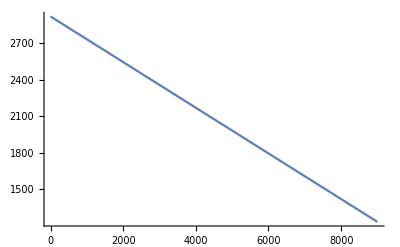

```mathematica
Plot[fbal[x],{x,0,9000}]
```

```mathematica
plotbetaKSi
```

plotbetaKSi

```mathematica
Lvec
```

{0.,200.,400.,600.,800.,1000.,1200.,1400.,1600.,1800.,2000.,2200.,2400.,2600.,2800.,3000.,3200.,3400.,3600.,3800.,4000.,4200.,4400.,4600.,4800.,5000.,5200.,5400.,5600.,5800.,6000.,6200.,6400.,6600.,6800.,7000.,7200.,7400.,7600.,7800.,8000.,8200.,8400.,8600.,8800.,9000.,9200.,9400.,9600.,9800.,10000.,10200.,10400.,10600.,10800.,11000.,11200.,11400.,11600.,11800.,12000.,12200.,12400.,12600.,12800.,13000.,13200.,13400.,13600.,13800.,14000.,14200.,14400.,14600.,14800.,15000.}

```mathematica
(*tab=Transpose[{Lvec,Fi,Ffinal}];
PrependTo[tab,{"Depth (ft)"," Initial Axial Forcelbf)"," Kick Axial Force(lbf)"}];
tabforce=TableForm[tab]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\tabforce.jpg",tabforce,ImageResolution->300]*)
```

```mathematica
(*Dados das variáveis aleatórias do modelo de Klever Stewart -  ISO 10400*)
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.01},{"Pext","NORMAL",1.0,0.01},{"Pint","NORMAL",1.0,0.01}};
(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];

(*Dados do tubular - (N80,OD=9 5/8, W=53.5 lb/ft, L =15000 ft*)

vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];
(*Cálculo de GX e GRADGX de Klever-Stewart*)
ComputeNumericalGradKS[vars[[3]],M]
(*Verificação do cálculo da derivada*)

(*Table[checkconv[vars[[i]],M,ComputeNumericalGradKS],{i,1,1}]*)
varsb=Table[{de,sigy,t,PIfim[[i]],PEfim[[i]]},{i,1,Length[PIfim]}];
plotbetaBarlow=Table[{HRLF[RVVec,RX,ComputeBurstBarlow,varsb[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];

(*FORM Para Klever-Stewart*)

plotbetaKS=Table[{HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,6,Length[Lvec]}];
(*plotbetaKSi=Table[{iHRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,6,Length[Lvec]}];*)
(*beta=Table[plotbetaKS[[i,1]],{i,1,Length[plotbetaKS]}];
beta2=Table[plotbetaKSi[[i,1]],{i,1,Length[plotbetaKSi]}];
(*Fator de Segurança Para Klever-Stewart*)

SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{SFBarlow,SFKS,plotbetaBarlow},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Barlow SF","Klever-Stewart Safety Factor","Reliability Index HRLF"},PlotMarkers->{"X","O","□", "◇","I"}]*)
```

Ductile rupture

Ductile rupture

Ductile rupture

«10 more identical outputs»

{9817.96,{10293.7,9351.53,10479.5,175.612,605.135,-818.183}}

| iter = 8  | residual = 0.00013597 | G(x) = -0.000388981| Beta = 20.1481

| iter = 8  | residual = 0.0001024 | G(x) = -0.000331988| Beta = 20.0689

| iter = 8  | residual = 0.000077734 | G(x) = -0.000284466| Beta = 19.9895

| iter = 7  | residual = 0.000585946 | G(x) = -0.0211416| Beta = 19.9099

| iter = 7  | residual = 0.000400818 | G(x) = -0.0168624| Beta = 19.8299

| iter = 8  | residual = 0.0000412451 | G(x) = -0.00021432| Beta = 19.7497

| iter = 8  | residual = 0.0000377367 | G(x) = -0.00021867| Beta = 19.6693

| iter = 8  | residual = 0.0000374777 | G(x) = -0.000240425| Beta = 19.5887

| iter = 8  | residual = 0.000040352 | G(x) = -0.000284409| Beta = 19.5078

| iter = 8  | residual = 0.0000465909 | G(x) = -0.000358446| Beta = 19.4267

| iter = 8  | residual = 0.0000567585 | G(x) = -0.000474299| Beta = 19.3453

| iter = 8  | residual = 0.0000717345 | G(x) = -0.000648708| Beta = 19.2636

| iter = 8  | residual = 0.0000926966 | G(x) = -0.000904494| Beta = 19.1818

| iter = 8  | residual = 0.000121101 | G(x) = -0.00127177| Beta = 19.0996

| iter = 8  | residual = 0.000158663 | G(x) = -0.00178919| Beta = 19.0172

| iter = 8  | residual = 0.000207335 | G(x) = -0.00250524| Beta = 18.9346

| iter = 8  | residual = 0.000269283 | G(x) = -0.00347945| Beta = 18.8517

| iter = 8  | residual = 0.000346849 | G(x) = -0.00478354| Beta = 18.7685

| iter = 8  | residual = 0.000442509 | G(x) = -0.0065023| Beta = 18.6851

| iter = 8  | residual = 0.000558821 | G(x) = -0.00873413| Beta = 18.6015

| iter = 8  | residual = 0.000698349 | G(x) = -0.0115911| Beta = 18.5175

| iter = 8  | residual = 0.000863585 | G(x) = -0.0151986| Beta = 18.4334

| iter = 9  | residual = 0.0000671722 | G(x) = -0.00125278| Beta = 18.3489

| iter = 9  | residual = 0.0000869063 | G(x) = -0.00171067| Beta = 18.2642

| iter = 9  | residual = 0.000111176 | G(x) = -0.00230644| Beta = 18.1792

| iter = 9  | residual = 0.000140669 | G(x) = -0.00307157| Beta = 18.094

| iter = 9  | residual = 0.00017609 | G(x) = -0.00404181| Beta = 18.0085

| iter = 9  | residual = 0.000218141 | G(x) = -0.00525694| Beta = 17.9228

| iter = 9  | residual = 0.000267498 | G(x) = -0.00676033| Beta = 17.8368

| iter = 9  | residual = 0.000324778 | G(x) = -0.00859814| Beta = 17.7506

| iter = 9  | residual = 0.00039051 | G(x) = -0.0108183| Beta = 17.6641

| iter = 9  | residual = 0.000465097 | G(x) = -0.0134688| Beta = 17.5773

| iter = 9  | residual = 0.000548784 | G(x) = -0.0165965| Beta = 17.4903

| iter = 9  | residual = 0.000641624 | G(x) = -0.0202443| Beta = 17.4031

| iter = 9  | residual = 0.000743447 | G(x) = -0.0244492| Beta = 17.3156

| iter = 9  | residual = 0.000853832 | G(x) = -0.0292397| Beta = 17.2279

| iter = 9  | residual = 0.000972092 | G(x) = -0.0346332| Beta = 17.1399

| iter = 10  | residual = 0.000159826 | G(x) = -0.00585061| Beta = 17.0515

| iter = 10  | residual = 0.000187545 | G(x) = -0.00712025| Beta = 16.963

| iter = 10  | residual = 0.000218026 | G(x) = -0.00857699| Beta = 16.8743

| iter = 10  | residual = 0.000251126 | G(x) = -0.0102274| Beta = 16.7853

| iter = 10  | residual = 0.000286614 | G(x) = -0.0120732| Beta = 16.6961

| iter = 10  | residual = 0.000324161 | G(x) = -0.0141107| Beta = 16.6067

| iter = 10  | residual = 0.000363344 | G(x) = -0.0163295| Beta = 16.5171

| iter = 10  | residual = 0.000403648 | G(x) = -0.0187124| Beta = 16.4272

| iter = 10  | residual = 0.000444481 | G(x) = -0.0212348| Beta = 16.3372

| iter = 10  | residual = 0.000485181 | G(x) = -0.0238651| Beta = 16.2469

| iter = 10  | residual = 0.000525041 | G(x) = -0.0265647| Beta = 16.1565

| iter = 10  | residual = 0.000600294 | G(x) = -0.0320653| Beta = 15.9724

| iter = 10  | residual = 0.000688586 | G(x) = -0.0396058| Beta = 15.6936

| iter = 10  | residual = 0.000733141 | G(x) = -0.0449669| Beta = 15.4135

| iter = 10  | residual = 0.000727619 | G(x) = -0.0471145| Beta = 15.1322

| iter = 10  | residual = 0.000676497 | G(x) = -0.0457783| Beta = 14.8501

| iter = 10  | residual = 0.000592476 | G(x) = -0.0414833| Beta = 14.5676

| iter = 10  | residual = 0.000491649 | G(x) = -0.0352785| Beta = 14.285

| iter = 10  | residual = 0.000388855 | G(x) = -0.0283403| Beta = 14.0029

| iter = 9  | residual = 0.000845591 | G(x) = -0.0626802| Beta = 13.722

| iter = 9  | residual = 0.000623781 | G(x) = -0.0461484| Beta = 13.4418

| iter = 9  | residual = 0.000449704 | G(x) = -0.0329995| Beta = 13.1632

| iter = 8  | residual = 0.000951059 | G(x) = -0.0694007| Beta = 12.8868

| iter = 8  | residual = 0.000684487 | G(x) = -0.0489571| Beta = 12.6121

| iter = 8  | residual = 0.000487912 | G(x) = -0.0340776| Beta = 12.3397

| iter = 8  | residual = 0.000344869 | G(x) = -0.0234449| Beta = 12.0697

| iter = 7  | residual = 0.000849821 | G(x) = -0.0563743| Beta = 11.8024

| iter = 7  | residual = 0.000624413 | G(x) = -0.0400554| Beta = 11.5375

| iter = 7  | residual = 0.000457096 | G(x) = -0.0282985| Beta = 11.2752

| iter = 7  | residual = 0.000333441 | G(x) = -0.0198862| Beta = 11.0155

| iter = 7  | residual = 0.00024242 | G(x) = -0.0139044| Beta = 10.7585

| iter = 6  | residual = 0.000816561 | G(x) = -0.0451241| Beta = 10.5042

| iter = 6  | residual = 0.000628122 | G(x) = -0.0332589| Beta = 10.2523

| iter = 6  | residual = 0.000482138 | G(x) = -0.0244305| Beta = 10.003

| iter = 6  | residual = 0.000369255 | G(x) = -0.0178836| Beta = 9.75614

| iter = 6  | residual = 0.000282134 | G(x) = -0.0130445| Beta = 9.51176

| iter = 6  | residual = 0.00021503 | G(x) = -0.00947983| Beta = 9.2698

| iter = 6  | residual = 0.000163453 | G(x) = -0.00686288| Beta = 9.0302

| iter = 5  | residual = 0.00089786 | G(x) = -0.0365039| Beta = 8.79303

Ductile rupture

Ductile rupture

Ductile rupture

«101 more identical outputs»

| iter = 8  | residual = 0.000122498 | G(x) = -0.000600909| Beta = 20.0251

Ductile rupture

Ductile rupture

Ductile rupture

«101 more identical outputs»

| iter = 8  | residual = 0.0000801483 | G(x) = -0.000424093| Beta = 19.9761

Ductile rupture

Ductile rupture

Ductile rupture

«101 more identical outputs»

| iter = 8  | residual = 0.0000438666 | G(x) = -0.000249425| Beta = 19.9281

Ductile rupture

Ductile rupture

Ductile rupture

«101 more identical outputs»

| iter = 8  | residual = 0.0000216269 | G(x) = -0.0001321| Beta = 19.881

Ductile rupture

Ductile rupture

Ductile rupture

«101 more identical outputs»

| iter = 8  | residual = 0.0000100158 | G(x) = -0.0000660457| Beta = 19.8348

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.000637229 | G(x) = -0.00204189| Beta = 19.7896

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.000356196 | G(x) = -0.000933557| Beta = 19.7451

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0001911 | G(x) = -0.000454472| Beta = 19.7016

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000974591 | G(x) = -0.000253169| Beta = 19.6589

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000455549 | G(x) = -0.000171224| Beta = 19.6169

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000170781 | G(x) = -0.00014098| Beta = 19.5758

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 1.37063×10^-6 | G(x) = -0.000134214| Beta = 19.5355

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 7.49801×10^-6 | G(x) = -0.000138783| Beta = 19.4959

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000127014 | G(x) = -0.000148831| Beta = 19.457

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000112179 | G(x) = -0.00782902| Beta = 19.4189

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000526936 | G(x) = -0.00902383| Beta = 19.3815

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000903209 | G(x) = -0.0097872| Beta = 19.3447

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000197059 | G(x) = -0.000192231| Beta = 19.3086

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000199064 | G(x) = -0.000197783| Beta = 19.2731

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000197564 | G(x) = -0.000200438| Beta = 19.2383

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000193266 | G(x) = -0.00020034| Beta = 19.2041

Ductile rupture

Ductile rupture

Ductile rupture

«88 more identical outputs»

| iter = 7  | residual = 0.0000186793 | G(x) = -0.000197791| Beta = 19.1704

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000971459 | G(x) = -0.00977674| Beta = 19.1374

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000878343 | G(x) = -0.00936283| Beta = 19.105

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000683174 | G(x) = -0.423043| Beta = 19.0738

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000697999 | G(x) = -0.00840848| Beta = 19.0417

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000616311 | G(x) = -0.0079025| Beta = 19.0108

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000541921 | G(x) = -0.00739513| Beta = 18.9805

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000475125 | G(x) = -0.00689615| Beta = 18.9506

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000415789 | G(x) = -0.0064129| Beta = 18.9213

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000363518 | G(x) = -0.00595059| Beta = 18.8924

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000317773 | G(x) = -0.00551272| Beta = 18.8639

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000277948 | G(x) = -0.00510136| Beta = 18.836

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000243423 | G(x) = -0.00471749| Beta = 18.8084

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000213593 | G(x) = -0.00436123| Beta = 18.7813

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000187889 | G(x) = -0.00403208| Beta = 18.7546

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000165786 | G(x) = -0.0037291| Beta = 18.7284

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000146812 | G(x) = -0.00345103| Beta = 18.7025

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000130543 | G(x) = -0.00319643| Beta = 18.677

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000116605 | G(x) = -0.00296373| Beta = 18.6519

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000104671 | G(x) = -0.00275136| Beta = 18.6271

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000944536 | G(x) = -0.00255772| Beta = 18.6027

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000857054 | G(x) = -0.00238129| Beta = 18.5787

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000880154 | G(x) = -0.00231459| Beta = 18.5127

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000978894 | G(x) = -0.00232628| Beta = 18.3971

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000105643 | G(x) = -0.00233169| Beta = 18.2826

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000111602 | G(x) = -0.00233097| Beta = 18.169

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.00011604 | G(x) = -0.00232429| Beta = 18.0566

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000119184 | G(x) = -0.00231189| Beta = 17.9451

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000121228 | G(x) = -0.00229402| Beta = 17.8347

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000122336 | G(x) = -0.00227101| Beta = 17.7252

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000122649 | G(x) = -0.00224317| Beta = 17.6168

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000122287 | G(x) = -0.00221087| Beta = 17.5093

Ductile rupture

Ductile rupture

Ductile rupture

«3 more identical outputs»

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Ductile rupture

Ductile rupture

Ductile rupture

«69 more identical outputs»

| iter = 6  | residual = 0.000121354 | G(x) = -0.0021745| Beta = 17.4029

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000920715 | G(x) = -0.0800132| Beta = 17.2975

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000509074 | G(x) = -0.079563| Beta = 17.193

Ductile rupture

Ductile rupture

Ductile rupture

«5 more identical outputs»

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Ductile rupture

Ductile rupture

Ductile rupture

«32 more identical outputs»

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Ductile rupture

Ductile rupture

Ductile rupture

«19 more identical outputs»

| iter = 5  | residual = 0.000149903 | G(x) = -0.0788165| Beta = 17.0895

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000162439 | G(x) = -0.0778195| Beta = 16.9869

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000433014 | G(x) = -0.0766119| Beta = 16.8853

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000666364 | G(x) = -0.0752288| Beta = 16.7845

Ductile rupture

Ductile rupture

Ductile rupture

«62 more identical outputs»

| iter = 5  | residual = 0.000866563 | G(x) = -0.0737008| Beta = 16.6848

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000102017 | G(x) = -0.00178329| Beta = 16.5858

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000988697 | G(x) = -0.00172742| Beta = 16.4878

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000956742 | G(x) = -0.00167108| Beta = 16.3908

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000924537 | G(x) = -0.00161455| Beta = 16.2946

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000892279 | G(x) = -0.00155807| Beta = 16.1994

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000860138 | G(x) = -0.00150188| Beta = 16.1049

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.000082826 | G(x) = -0.00144618| Beta = 16.0114

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000796768 | G(x) = -0.00139113| Beta = 15.9187

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000765769 | G(x) = -0.00133691| Beta = 15.8269

Ductile rupture

Ductile rupture

Ductile rupture

«75 more identical outputs»

| iter = 6  | residual = 0.0000735348 | G(x) = -0.00128365| Beta = 15.7358

```mathematica
1
```

| iter = 7  | residual = 0.000400818 | G(x) = -0.0168624| Beta = 19.8299

| iter = 8  | residual = 0.0000412451 | G(x) = -0.00021432| Beta = 19.7497

| iter = 8  | residual = 0.0000377367 | G(x) = -0.00021867| Beta = 19.6693

| iter = 8  | residual = 0.0000374777 | G(x) = -0.000240425| Beta = 19.5887

| iter = 8  | residual = 0.000040352 | G(x) = -0.000284409| Beta = 19.5078

| iter = 8  | residual = 0.0000465909 | G(x) = -0.000358446| Beta = 19.4267

| iter = 8  | residual = 0.0000567585 | G(x) = -0.000474299| Beta = 19.3453

| iter = 8  | residual = 0.0000717345 | G(x) = -0.000648708| Beta = 19.2636

| iter = 8  | residual = 0.0000926966 | G(x) = -0.000904494| Beta = 19.1818

| iter = 8  | residual = 0.000121101 | G(x) = -0.00127177| Beta = 19.0996

| iter = 8  | residual = 0.000158663 | G(x) = -0.00178919| Beta = 19.0172

| iter = 8  | residual = 0.000207335 | G(x) = -0.00250524| Beta = 18.9346

| iter = 8  | residual = 0.000269283 | G(x) = -0.00347945| Beta = 18.8517

| iter = 8  | residual = 0.000346849 | G(x) = -0.00478354| Beta = 18.7685

| iter = 8  | residual = 0.000442509 | G(x) = -0.0065023| Beta = 18.6851

| iter = 8  | residual = 0.000558821 | G(x) = -0.00873413| Beta = 18.6015

| iter = 8  | residual = 0.000698349 | G(x) = -0.0115911| Beta = 18.5175

| iter = 8  | residual = 0.000863585 | G(x) = -0.0151986| Beta = 18.4334

| iter = 9  | residual = 0.0000671722 | G(x) = -0.00125278| Beta = 18.3489

| iter = 9  | residual = 0.0000869063 | G(x) = -0.00171067| Beta = 18.2642

| iter = 9  | residual = 0.000111176 | G(x) = -0.00230644| Beta = 18.1792

| iter = 9  | residual = 0.000140669 | G(x) = -0.00307157| Beta = 18.094

| iter = 9  | residual = 0.00017609 | G(x) = -0.00404181| Beta = 18.0085

| iter = 9  | residual = 0.000218141 | G(x) = -0.00525694| Beta = 17.9228

| iter = 9  | residual = 0.000267498 | G(x) = -0.00676033| Beta = 17.8368

| iter = 9  | residual = 0.000324778 | G(x) = -0.00859814| Beta = 17.7506

| iter = 9  | residual = 0.00039051 | G(x) = -0.0108183| Beta = 17.6641

| iter = 9  | residual = 0.000465097 | G(x) = -0.0134688| Beta = 17.5773

| iter = 9  | residual = 0.000548784 | G(x) = -0.0165965| Beta = 17.4903

| iter = 9  | residual = 0.000641624 | G(x) = -0.0202443| Beta = 17.4031

| iter = 9  | residual = 0.000743447 | G(x) = -0.0244492| Beta = 17.3156

| iter = 9  | residual = 0.000853832 | G(x) = -0.0292397| Beta = 17.2279

| iter = 9  | residual = 0.000972092 | G(x) = -0.0346332| Beta = 17.1399

| iter = 10  | residual = 0.000159826 | G(x) = -0.00585061| Beta = 17.0515

| iter = 10  | residual = 0.000187545 | G(x) = -0.00712025| Beta = 16.963

| iter = 10  | residual = 0.000218026 | G(x) = -0.00857699| Beta = 16.8743

| iter = 10  | residual = 0.000251126 | G(x) = -0.0102274| Beta = 16.7853

| iter = 10  | residual = 0.000286614 | G(x) = -0.0120732| Beta = 16.6961

| iter = 10  | residual = 0.000324161 | G(x) = -0.0141107| Beta = 16.6067

| iter = 10  | residual = 0.000363344 | G(x) = -0.0163295| Beta = 16.5171

| iter = 10  | residual = 0.000403648 | G(x) = -0.0187124| Beta = 16.4272

| iter = 10  | residual = 0.000444481 | G(x) = -0.0212348| Beta = 16.3372

| iter = 10  | residual = 0.000485181 | G(x) = -0.0238651| Beta = 16.2469

| iter = 10  | residual = 0.000525041 | G(x) = -0.0265647| Beta = 16.1565

| iter = 10  | residual = 0.000600294 | G(x) = -0.0320653| Beta = 15.9724

| iter = 10  | residual = 0.000688586 | G(x) = -0.0396058| Beta = 15.6936

| iter = 10  | residual = 0.000733141 | G(x) = -0.0449669| Beta = 15.4135

| iter = 10  | residual = 0.000727619 | G(x) = -0.0471145| Beta = 15.1322

| iter = 10  | residual = 0.000676497 | G(x) = -0.0457783| Beta = 14.8501

| iter = 10  | residual = 0.000592476 | G(x) = -0.0414833| Beta = 14.5676

| iter = 10  | residual = 0.000491649 | G(x) = -0.0352785| Beta = 14.285

| iter = 10  | residual = 0.000388855 | G(x) = -0.0283403| Beta = 14.0029

| iter = 9  | residual = 0.000845591 | G(x) = -0.0626802| Beta = 13.722

| iter = 9  | residual = 0.000623781 | G(x) = -0.0461484| Beta = 13.4418

| iter = 9  | residual = 0.000449704 | G(x) = -0.0329995| Beta = 13.1632

| iter = 8  | residual = 0.000951059 | G(x) = -0.0694007| Beta = 12.8868

| iter = 8  | residual = 0.000684487 | G(x) = -0.0489571| Beta = 12.6121

| iter = 8  | residual = 0.000487912 | G(x) = -0.0340776| Beta = 12.3397

| iter = 8  | residual = 0.000344869 | G(x) = -0.0234449| Beta = 12.0697

| iter = 7  | residual = 0.000849821 | G(x) = -0.0563743| Beta = 11.8024

| iter = 7  | residual = 0.000624413 | G(x) = -0.0400554| Beta = 11.5375

| iter = 7  | residual = 0.000457096 | G(x) = -0.0282985| Beta = 11.2752

| iter = 7  | residual = 0.000333441 | G(x) = -0.0198862| Beta = 11.0155

| iter = 7  | residual = 0.00024242 | G(x) = -0.0139044| Beta = 10.7585

| iter = 6  | residual = 0.000816561 | G(x) = -0.0451241| Beta = 10.5042

| iter = 6  | residual = 0.000628122 | G(x) = -0.0332589| Beta = 10.2523

| iter = 6  | residual = 0.000482138 | G(x) = -0.0244305| Beta = 10.003

| iter = 6  | residual = 0.000369255 | G(x) = -0.0178836| Beta = 9.75614

| iter = 6  | residual = 0.000282134 | G(x) = -0.0130445| Beta = 9.51176

| iter = 6  | residual = 0.00021503 | G(x) = -0.00947983| Beta = 9.2698

| iter = 6  | residual = 0.000163453 | G(x) = -0.00686288| Beta = 9.0302

| iter = 5  | residual = 0.00089786 | G(x) = -0.0365039| Beta = 8.79303

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.136364 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247])) (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+100. (0.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+100. (0.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+21.5424 (0.+(0.04642 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2] | G(x) = -1363.64 (1.-(0.136364 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2))+753.247 (1.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247])) (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)),80000 (1.1+(0.04642 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)),37742.6 (1.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)),753.247 (1.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2))]| Beta = √((0.+100. (0.-(0.136364 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247])) (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+100. (0.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+100. (0.+(0.01 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+21.5424 (0.+(0.04642 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (610.39-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247])))/(185.951+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]))^2+(0.+10. (0.753247-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,754.001]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37780.4,753.247]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37742.6,753.247]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37742.6,753.247]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37742.6,753.247]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.154546 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897])) (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+100. (0.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+100. (0.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+21.5424 (0.+(0.04642 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2] | G(x) = -1545.46 (1.-(0.154546 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2))+903.897 (1.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897])) (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)),80000 (1.1+(0.04642 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)),37054.4 (1.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)),903.897 (1.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2))]| Beta = √((0.+100. (0.-(0.154546 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897])) (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+100. (0.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+100. (0.+(0.01 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+21.5424 (0.+(0.04642 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (641.559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897])))/(238.843+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]))^2+(0.+10. (0.903897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,904.801]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37091.4,903.897]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,37054.4,903.897]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,37054.4,903.897]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,37054.4,903.897]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.172727 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55])) (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+100. (0.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+100. (0.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+21.5424 (0.+(0.04642 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2] | G(x) = -1727.27 (1.-(0.172727 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2))+1054.55 (1.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55])) (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)),80000 (1.1+(0.04642 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)),36366.1 (1.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)),1054.55 (1.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2))]| Beta = √((0.+100. (0.-(0.172727 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55])) (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+100. (0.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+100. (0.+(0.01 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+21.5424 (0.+(0.04642 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (672.728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55])))/(298.348+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]))^2+(0.+10. (1.05455-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1055.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36402.5,1054.55]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,36366.1,1054.55]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,36366.1,1054.55]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,36366.1,1054.55]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.190909 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2])) (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+100. (0.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+100. (0.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+21.5424 (0.+(0.04642 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2] | G(x) = -1909.09 (1.-(0.190909 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2))+1205.2 (1.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2])) (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)),80000 (1.1+(0.04642 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)),35677.8 (1.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)),1205.2 (1.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2))]| Beta = √((0.+100. (0.-(0.190909 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2])) (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+100. (0.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+100. (0.+(0.01 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+21.5424 (0.+(0.04642 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (703.897-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2])))/(364.463+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]))^2+(0.+10. (1.2052-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1206.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35713.5,1205.2]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,35677.8,1205.2]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35677.8,1205.2]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,35677.8,1205.2]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.209091 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85])) (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+100. (0.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+100. (0.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2] | G(x) = -2090.91 (1.-(0.209091 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2))+1355.85 (1.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85])) (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)),80000 (1.1+(0.04642 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)),34989.6 (1.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)),1355.85 (1.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2))]| Beta = √((0.+100. (0.-(0.209091 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85])) (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+100. (0.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+100. (0.+(0.01 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (735.066-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85])))/(437.191+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]))^2+(0.+10. (1.35585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1357.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,35024.6,1355.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34989.6,1355.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34989.6,1355.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34989.6,1355.85]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.227273 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49])) (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+100. (0.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+100. (0.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2] | G(x) = -2272.73 (1.-(0.227273 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2))+1506.49 (1.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49])) (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)),80000 (1.1+(0.04642 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)),34301.3 (1.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)),1506.49 (1.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2))]| Beta = √((0.+100. (0.-(0.227273 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49])) (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+100. (0.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+100. (0.+(0.01 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (766.234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49])))/(516.53+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]))^2+(0.+10. (1.50649-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1508.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34335.6,1506.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,34301.3,1506.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,34301.3,1506.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,34301.3,1506.49]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.245455 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14])) (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+100. (0.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+100. (0.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+21.5424 (0.+(0.04642 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2] | G(x) = -2454.55 (1.-(0.245455 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2))+1657.14 (1.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14])) (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)),80000 (1.1+(0.04642 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)),33613.1 (1.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)),1657.14 (1.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2))]| Beta = √((0.+100. (0.-(0.245455 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14])) (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+100. (0.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+100. (0.+(0.01 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+21.5424 (0.+(0.04642 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (797.403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14])))/(602.48+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]))^2+(0.+10. (1.65714-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1658.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33646.7,1657.14]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,33613.1,1657.14]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,33613.1,1657.14]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,33613.1,1657.14]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.263637 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79])) (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+100. (0.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+100. (0.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+21.5424 (0.+(0.04642 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2] | G(x) = -2636.37 (1.-(0.263637 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2))+1807.79 (1.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79])) (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)),80000 (1.1+(0.04642 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)),32924.8 (1.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)),1807.79 (1.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2))]| Beta = √((0.+100. (0.-(0.263637 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79])) (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+100. (0.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+100. (0.+(0.01 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+21.5424 (0.+(0.04642 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (828.572-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79])))/(695.043+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]))^2+(0.+10. (1.80779-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1809.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32957.7,1807.79]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32924.8,1807.79]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32924.8,1807.79]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32924.8,1807.79]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.281818 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44])) (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+100. (0.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+100. (0.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+21.5424 (0.+(0.04642 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2] | G(x) = -2818.18 (1.-(0.281818 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2))+1958.44 (1.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44])) (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)),80000 (1.1+(0.04642 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)),32236.5 (1.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)),1958.44 (1.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2))]| Beta = √((0.+100. (0.-(0.281818 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44])) (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+100. (0.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+100. (0.+(0.01 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+21.5424 (0.+(0.04642 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (859.741-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44])))/(794.216+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]))^2+(0.+10. (1.95844-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1960.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32268.8,1958.44]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,32236.5,1958.44]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,32236.5,1958.44]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,32236.5,1958.44]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.3 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09])) (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+100. (0.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+100. (0.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+21.5424 (0.+(0.04642 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2] | G(x) = -3000. (1.-(0.3 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2))+2109.09 (1.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09])) (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)),80000 (1.1+(0.04642 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)),31548.3 (1.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)),2109.09 (1.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2))]| Beta = √((0.+100. (0.-(0.3 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09])) (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+100. (0.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+100. (0.+(0.01 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+21.5424 (0.+(0.04642 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (890.91-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09])))/(900.002+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]))^2+(0.+10. (2.10909-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2111.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31579.8,2109.09]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,31548.3,2109.09]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,31548.3,2109.09]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,31548.3,2109.09]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.318182 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74])) (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+100. (0.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+100. (0.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+21.5424 (0.+(0.04642 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2] | G(x) = -3181.82 (1.-(0.318182 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2))+2259.74 (1.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74])) (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)),80000 (1.1+(0.04642 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)),30860. (1.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)),2259.74 (1.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2))]| Beta = √((0.+100. (0.-(0.318182 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74])) (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+100. (0.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+100. (0.+(0.01 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+21.5424 (0.+(0.04642 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (922.079-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74])))/(1012.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]))^2+(0.+10. (2.25974-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2262.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30890.9,2259.74]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30860.,2259.74]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30860.,2259.74]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30860.,2259.74]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.336364 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39])) (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+100. (0.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+100. (0.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+21.5424 (0.+(0.04642 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2] | G(x) = -3363.64 (1.-(0.336364 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2))+2410.39 (1.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39])) (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)),80000 (1.1+(0.04642 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)),30171.8 (1.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)),2410.39 (1.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2))]| Beta = √((0.+100. (0.-(0.336364 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39])) (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+100. (0.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+100. (0.+(0.01 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+21.5424 (0.+(0.04642 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (953.248-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39])))/(1131.41+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]))^2+(0.+10. (2.41039-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2412.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30201.9,2410.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,30171.8,2410.39]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,30171.8,2410.39]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,30171.8,2410.39]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.354546 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04])) (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+100. (0.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+100. (0.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+21.5424 (0.+(0.04642 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2] | G(x) = -3545.46 (1.-(0.354546 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2))+2561.04 (1.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04])) (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)),80000 (1.1+(0.04642 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)),29483.5 (1.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)),2561.04 (1.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2))]| Beta = √((0.+100. (0.-(0.354546 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04])) (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+100. (0.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+100. (0.+(0.01 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+21.5424 (0.+(0.04642 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (984.416-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04])))/(1257.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]))^2+(0.+10. (2.56104-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2563.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29513.,2561.04]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,29483.5,2561.04]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,29483.5,2561.04]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,29483.5,2561.04]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.372728 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69])) (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+100. (0.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+100. (0.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2] | G(x) = -3727.28 (1.-(0.372728 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2))+2711.69 (1.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69])) (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)),80000 (1.1+(0.04642 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)),28795.3 (1.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)),2711.69 (1.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2))]| Beta = √((0.+100. (0.-(0.372728 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69])) (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+100. (0.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+100. (0.+(0.01 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1015.59-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69])))/(1389.26+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]))^2+(0.+10. (2.71169-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2714.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28824.,2711.69]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28795.3,2711.69]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28795.3,2711.69]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28795.3,2711.69]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.390909 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34])) (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+100. (0.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+100. (0.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2] | G(x) = -3909.09 (1.-(0.390909 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2))+2862.34 (1.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34])) (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)),80000 (1.1+(0.04642 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)),28107. (1.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)),2862.34 (1.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2))]| Beta = √((0.+100. (0.-(0.390909 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34])) (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+100. (0.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+100. (0.+(0.01 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1046.75-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34])))/(1528.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]))^2+(0.+10. (2.86234-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2865.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28135.1,2862.34]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,28107.,2862.34]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,28107.,2862.34]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,28107.,2862.34]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.409091 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99])) (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+100. (0.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+100. (0.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2] | G(x) = -4090.91 (1.-(0.409091 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2))+3012.99 (1.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99])) (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)),80000 (1.1+(0.04642 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)),27418.7 (1.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)),3012.99 (1.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2))]| Beta = √((0.+100. (0.-(0.409091 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99])) (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+100. (0.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+100. (0.+(0.01 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1077.92-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99])))/(1673.56+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]))^2+(0.+10. (3.01299-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3016.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27446.2,3012.99]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,27418.7,3012.99]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,27418.7,3012.99]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,27418.7,3012.99]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.427273 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64])) (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+100. (0.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+100. (0.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2] | G(x) = -4272.73 (1.-(0.427273 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2))+3163.64 (1.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64])) (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)),80000 (1.1+(0.04642 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)),26730.5 (1.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)),3163.64 (1.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2))]| Beta = √((0.+100. (0.-(0.427273 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64])) (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+100. (0.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+100. (0.+(0.01 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1109.09-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64])))/(1825.62+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]))^2+(0.+10. (3.16364-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3166.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26757.2,3163.64]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26730.5,3163.64]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26730.5,3163.64]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26730.5,3163.64]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.445455 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29])) (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+100. (0.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+100. (0.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2] | G(x) = -4454.55 (1.-(0.445455 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2))+3314.29 (1.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29])) (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)),80000 (1.1+(0.04642 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)),26042.2 (1.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)),3314.29 (1.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2))]| Beta = √((0.+100. (0.-(0.445455 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29])) (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+100. (0.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+100. (0.+(0.01 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1140.26-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29])))/(1984.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]))^2+(0.+10. (3.31429-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3317.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26068.3,3314.29]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,26042.2,3314.29]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,26042.2,3314.29]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,26042.2,3314.29]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.463637 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94])) (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+100. (0.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+100. (0.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2] | G(x) = -4636.37 (1.-(0.463637 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2))+3464.94 (1.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94])) (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)),80000 (1.1+(0.04642 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)),25354. (1.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)),3464.94 (1.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2))]| Beta = √((0.+100. (0.-(0.463637 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94])) (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+100. (0.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+100. (0.+(0.01 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1171.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94])))/(2149.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]))^2+(0.+10. (3.46494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3468.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25379.3,3464.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,25354.,3464.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,25354.,3464.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,25354.,3464.94]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.481819 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59])) (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+100. (0.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+100. (0.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2] | G(x) = -4818.19 (1.-(0.481819 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2))+3615.59 (1.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59])) (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)),80000 (1.1+(0.04642 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)),24665.7 (1.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)),3615.59 (1.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2))]| Beta = √((0.+100. (0.-(0.481819 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59])) (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+100. (0.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+100. (0.+(0.01 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1202.6-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59])))/(2321.49+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]))^2+(0.+10. (3.61559-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3619.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24690.4,3615.59]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,24665.7,3615.59]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24665.7,3615.59]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,24665.7,3615.59]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.5 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24])) (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+100. (0.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+100. (0.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2] | G(x) = -5000. (1.-(0.5 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2))+3766.24 (1.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24])) (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)),80000 (1.1+(0.04642 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)),23977.4 (1.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)),3766.24 (1.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2))]| Beta = √((0.+100. (0.-(0.5 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24])) (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+100. (0.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+100. (0.+(0.01 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1233.77-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24])))/(2500.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]))^2+(0.+10. (3.76624-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3770.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,24001.4,3766.24]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23977.4,3766.24]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23977.4,3766.24]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23977.4,3766.24]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.518182 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89])) (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+100. (0.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+100. (0.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2] | G(x) = -5181.82 (1.-(0.518182 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2))+3916.89 (1.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89])) (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)),80000 (1.1+(0.04642 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)),23289.2 (1.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)),3916.89 (1.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2))]| Beta = √((0.+100. (0.-(0.518182 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89])) (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+100. (0.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+100. (0.+(0.01 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1264.94-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89])))/(2685.13+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]))^2+(0.+10. (3.91689-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3920.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23312.5,3916.89]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,23289.2,3916.89]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,23289.2,3916.89]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,23289.2,3916.89]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.536364 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54])) (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+100. (0.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+100. (0.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2] | G(x) = -5363.64 (1.-(0.536364 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2))+4067.54 (1.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54])) (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)),80000 (1.1+(0.04642 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)),22600.9 (1.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)),4067.54 (1.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2))]| Beta = √((0.+100. (0.-(0.536364 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54])) (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+100. (0.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+100. (0.+(0.01 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1296.11-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54])))/(2876.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]))^2+(0.+10. (4.06754-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4071.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22623.5,4067.54]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,22600.9,4067.54]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,22600.9,4067.54]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,22600.9,4067.54]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.554546 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19])) (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+100. (0.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+100. (0.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2] | G(x) = -5545.46 (1.-(0.554546 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2))+4218.19 (1.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19])) (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)),80000 (1.1+(0.04642 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)),21912.7 (1.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)),4218.19 (1.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2))]| Beta = √((0.+100. (0.-(0.554546 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19])) (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+100. (0.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+100. (0.+(0.01 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1327.27-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19])))/(3075.21+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]))^2+(0.+10. (4.21819-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4222.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21934.6,4218.19]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21912.7,4218.19]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21912.7,4218.19]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21912.7,4218.19]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.572728 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84])) (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+100. (0.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+100. (0.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2] | G(x) = -5727.28 (1.-(0.572728 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2))+4368.84 (1.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84])) (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)),80000 (1.1+(0.04642 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)),21224.4 (1.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)),4368.84 (1.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2))]| Beta = √((0.+100. (0.-(0.572728 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84])) (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+100. (0.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+100. (0.+(0.01 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1358.44-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84])))/(3280.17+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]))^2+(0.+10. (4.36884-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4373.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21245.6,4368.84]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,21224.4,4368.84]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,21224.4,4368.84]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,21224.4,4368.84]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.59091 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48])) (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+100. (0.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+100. (0.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2] | G(x) = -5909.1 (1.-(0.59091 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2))+4519.48 (1.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48])) (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)),80000 (1.1+(0.04642 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)),20536.1 (1.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)),4519.48 (1.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2))]| Beta = √((0.+100. (0.-(0.59091 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48])) (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+100. (0.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+100. (0.+(0.01 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1389.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48])))/(3491.74+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]))^2+(0.+10. (4.51948-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4524.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20556.7,4519.48]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,20536.1,4519.48]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,20536.1,4519.48]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,20536.1,4519.48]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.609091 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13])) (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+100. (0.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+100. (0.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2] | G(x) = -6090.91 (1.-(0.609091 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2))+4670.13 (1.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13])) (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)),80000 (1.1+(0.04642 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)),19847.9 (1.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)),4670.13 (1.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2))]| Beta = √((0.+100. (0.-(0.609091 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13])) (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+100. (0.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+100. (0.+(0.01 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1420.78-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13])))/(3709.92+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]))^2+(0.+10. (4.67013-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4674.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19867.7,4670.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19847.9,4670.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19847.9,4670.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19847.9,4670.13]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.627273 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78])) (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+100. (0.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+100. (0.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2] | G(x) = -6272.73 (1.-(0.627273 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2))+4820.78 (1.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78])) (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)),80000 (1.1+(0.04642 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)),19159.6 (1.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)),4820.78 (1.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2))]| Beta = √((0.+100. (0.-(0.627273 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78])) (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+100. (0.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+100. (0.+(0.01 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1451.95-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78])))/(3934.72+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]))^2+(0.+10. (4.82078-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4825.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19178.8,4820.78]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,19159.6,4820.78]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,19159.6,4820.78]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,19159.6,4820.78]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.645455 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43])) (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+100. (0.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+100. (0.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2] | G(x) = -6454.55 (1.-(0.645455 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2))+4971.43 (1.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43])) (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)),80000 (1.1+(0.04642 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)),18471.4 (1.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)),4971.43 (1.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2))]| Beta = √((0.+100. (0.-(0.645455 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43])) (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+100. (0.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+100. (0.+(0.01 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1483.12-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43])))/(4166.12+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]))^2+(0.+10. (4.97143-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4976.4]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18489.8,4971.43]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,18471.4,4971.43]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,18471.4,4971.43]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,18471.4,4971.43]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.663637 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08])) (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+100. (0.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+100. (0.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2] | G(x) = -6636.37 (1.-(0.663637 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2))+5122.08 (1.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08])) (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)),80000 (1.1+(0.04642 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)),17783.1 (1.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)),5122.08 (1.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2))]| Beta = √((0.+100. (0.-(0.663637 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08])) (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+100. (0.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+100. (0.+(0.01 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1514.29-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08])))/(4404.14+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]))^2+(0.+10. (5.12208-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5127.2]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17800.9,5122.08]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17783.1,5122.08]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17783.1,5122.08]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17783.1,5122.08]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.681819 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73])) (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+100. (0.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+100. (0.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2] | G(x) = -6818.19 (1.-(0.681819 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2))+5272.73 (1.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73])) (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)),80000 (1.1+(0.04642 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)),17094.9 (1.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)),5272.73 (1.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2))]| Beta = √((0.+100. (0.-(0.681819 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73])) (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+100. (0.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+100. (0.+(0.01 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1545.46-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73])))/(4648.77+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]))^2+(0.+10. (5.27273-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5278.]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17112.,5272.73]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,17094.9,5272.73]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,17094.9,5272.73]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,17094.9,5272.73]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.700001 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38])) (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+100. (0.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+100. (0.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2] | G(x) = -7000.01 (1.-(0.700001 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2))+5423.38 (1.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38])) (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)),80000 (1.1+(0.04642 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)),16406.6 (1.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)),5423.38 (1.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2))]| Beta = √((0.+100. (0.-(0.700001 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38])) (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+100. (0.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+100. (0.+(0.01 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1576.62-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38])))/(4900.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]))^2+(0.+10. (5.42338-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5428.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16423.,5423.38]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,16406.6,5423.38]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,16406.6,5423.38]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,16406.6,5423.38]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.718182 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03])) (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+100. (0.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+100. (0.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2] | G(x) = -7181.82 (1.-(0.718182 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2))+5574.03 (1.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03])) (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)),80000 (1.1+(0.04642 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)),15718.3 (1.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)),5574.03 (1.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2))]| Beta = √((0.+100. (0.-(0.718182 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03])) (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+100. (0.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+100. (0.+(0.01 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1607.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03])))/(5157.86+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]))^2+(0.+10. (5.57403-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5579.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15734.1,5574.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15718.3,5574.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15718.3,5574.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15718.3,5574.03]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.736364 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68])) (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+100. (0.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+100. (0.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2] | G(x) = -7363.64 (1.-(0.736364 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2))+5724.68 (1.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68])) (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)),80000 (1.1+(0.04642 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)),15030.1 (1.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)),5724.68 (1.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2))]| Beta = √((0.+100. (0.-(0.736364 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68])) (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+100. (0.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+100. (0.+(0.01 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1638.96-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68])))/(5422.32+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]))^2+(0.+10. (5.72468-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5730.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15045.1,5724.68]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,15030.1,5724.68]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,15030.1,5724.68]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,15030.1,5724.68]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.754546 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33])) (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+100. (0.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+100. (0.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2] | G(x) = -7545.46 (1.-(0.754546 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2))+5875.33 (1.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33])) (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)),80000 (1.1+(0.04642 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)),14341.8 (1.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)),5875.33 (1.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2))]| Beta = √((0.+100. (0.-(0.754546 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33])) (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+100. (0.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+100. (0.+(0.01 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1670.13-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33])))/(5693.4+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]))^2+(0.+10. (5.87533-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5881.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14356.2,5875.33]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,14341.8,5875.33]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,14341.8,5875.33]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,14341.8,5875.33]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.772728 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98])) (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+100. (0.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+100. (0.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2] | G(x) = -7727.28 (1.-(0.772728 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2))+6025.98 (1.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98])) (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)),80000 (1.1+(0.04642 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)),13653.6 (1.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)),6025.98 (1.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2))]| Beta = √((0.+100. (0.-(0.772728 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98])) (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+100. (0.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+100. (0.+(0.01 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1701.3-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98])))/(5971.09+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]))^2+(0.+10. (6.02598-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6032.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13667.2,6025.98]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,13653.6,6025.98]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,13653.6,6025.98]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,13653.6,6025.98]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.79091 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63])) (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+100. (0.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+100. (0.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2] | G(x) = -7909.1 (1.-(0.79091 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2))+6176.63 (1.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63])) (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)),80000 (1.1+(0.04642 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)),12965.3 (1.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)),6176.63 (1.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2))]| Beta = √((0.+100. (0.-(0.79091 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63])) (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+100. (0.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+100. (0.+(0.01 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1732.47-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63])))/(6255.38+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]))^2+(0.+10. (6.17663-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6182.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12978.3,6176.63]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12965.3,6176.63]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12965.3,6176.63]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12965.3,6176.63]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.809092 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28])) (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+100. (0.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+100. (0.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2] | G(x) = -8090.92 (1.-(0.809092 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2))+6327.28 (1.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28])) (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)),80000 (1.1+(0.04642 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)),12277. (1.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)),6327.28 (1.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2))]| Beta = √((0.+100. (0.-(0.809092 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28])) (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+100. (0.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+100. (0.+(0.01 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1763.64-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28])))/(6546.29+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]))^2+(0.+10. (6.32728-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6333.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12289.3,6327.28]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,12277.,6327.28]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,12277.,6327.28]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,12277.,6327.28]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.827273 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93])) (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+100. (0.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+100. (0.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2] | G(x) = -8272.73 (1.-(0.827273 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2))+6477.93 (1.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93])) (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)),80000 (1.1+(0.04642 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)),11588.8 (1.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)),6477.93 (1.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2))]| Beta = √((0.+100. (0.-(0.827273 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93])) (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+100. (0.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+100. (0.+(0.01 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1794.81-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93])))/(6843.81+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]))^2+(0.+10. (6.47793-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6484.41]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11600.4,6477.93]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,11588.8,6477.93]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,11588.8,6477.93]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,11588.8,6477.93]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.845455 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58])) (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+100. (0.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+100. (0.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2] | G(x) = -8454.55 (1.-(0.845455 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2))+6628.58 (1.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58])) (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)),80000 (1.1+(0.04642 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)),10900.5 (1.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)),6628.58 (1.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2))]| Beta = √((0.+100. (0.-(0.845455 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58])) (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+100. (0.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+100. (0.+(0.01 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1825.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58])))/(7147.95+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]))^2+(0.+10. (6.62858-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6635.21]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10911.4,6628.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10900.5,6628.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10900.5,6628.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10900.5,6628.58]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.863637 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23])) (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+100. (0.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+100. (0.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2] | G(x) = -8636.37 (1.-(0.863637 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2))+6779.23 (1.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23])) (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)),80000 (1.1+(0.04642 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)),10212.3 (1.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)),6779.23 (1.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2))]| Beta = √((0.+100. (0.-(0.863637 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23])) (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+100. (0.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+100. (0.+(0.01 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1857.14-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23])))/(7458.69+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]))^2+(0.+10. (6.77923-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6786.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10222.5,6779.23]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,10212.3,6779.23]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,10212.3,6779.23]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,10212.3,6779.23]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.881819 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88])) (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+100. (0.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+100. (0.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2] | G(x) = -8818.19 (1.-(0.881819 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2))+6929.88 (1.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88])) (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)),80000 (1.1+(0.04642 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)),9524.01 (1.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)),6929.88 (1.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2))]| Beta = √((0.+100. (0.-(0.881819 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88])) (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+100. (0.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+100. (0.+(0.01 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1888.31-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88])))/(7776.05+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]))^2+(0.+10. (6.92988-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6936.81]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9533.54,6929.88]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9524.01,6929.88]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9524.01,6929.88]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9524.01,6929.88]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.900001 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53])) (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+100. (0.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+100. (0.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2] | G(x) = -9000.01 (1.-(0.900001 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2))+7080.53 (1.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53])) (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)),80000 (1.1+(0.04642 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)),8835.76 (1.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)),7080.53 (1.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2))]| Beta = √((0.+100. (0.-(0.900001 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53])) (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+100. (0.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+100. (0.+(0.01 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1919.48-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53])))/(8100.01+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]))^2+(0.+10. (7.08053-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7087.61]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8844.59,7080.53]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8835.76,7080.53]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8835.76,7080.53]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8835.76,7080.53]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.918183 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12])) (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+100. (0.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+100. (0.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2] | G(x) = -9181.83 (1.-(0.918183 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2))+7199.12 (1.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12])) (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)),80000 (1.1+(0.04642 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)),9922.36 (1.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)),7199.12 (1.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2))]| Beta = √((0.+100. (0.-(0.918183 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12])) (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+100. (0.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+100. (0.+(0.01 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+21.5424 (0.+(0.04642 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (1982.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12])))/(8430.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]))^2+(0.+10. (7.19912-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7206.32]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9932.28,7199.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9922.36,7199.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9922.36,7199.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9922.36,7199.12]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.936365 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67])) (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+100. (0.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+100. (0.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2] | G(x) = -9363.65 (1.-(0.936365 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2))+7285.67 (1.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67])) (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)),80000 (1.1+(0.04642 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)),9520.03 (1.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)),7285.67 (1.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2))]| Beta = √((0.+100. (0.-(0.936365 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67])) (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+100. (0.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+100. (0.+(0.01 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2077.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67])))/(8767.78+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]))^2+(0.+10. (7.28567-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7292.95]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9529.55,7285.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9520.03,7285.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9520.03,7285.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9520.03,7285.67]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.954546 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21])) (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+100. (0.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+100. (0.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2] | G(x) = -9545.46 (1.-(0.954546 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2))+7372.21 (1.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21])) (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)),80000 (1.1+(0.04642 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)),9117.7 (1.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)),7372.21 (1.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2))]| Beta = √((0.+100. (0.-(0.954546 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21])) (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+100. (0.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+100. (0.+(0.01 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2173.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21])))/(9111.59+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]))^2+(0.+10. (7.37221-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7379.59]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9126.82,7372.21]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,9117.7,7372.21]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,9117.7,7372.21]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,9117.7,7372.21]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.972728 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76])) (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+100. (0.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+100. (0.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2] | G(x) = -9727.28 (1.-(0.972728 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2))+7458.76 (1.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76])) (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)),80000 (1.1+(0.04642 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)),8715.38 (1.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)),7458.76 (1.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2))]| Beta = √((0.+100. (0.-(0.972728 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76])) (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+100. (0.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+100. (0.+(0.01 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2268.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76])))/(9462.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]))^2+(0.+10. (7.45876-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7466.22]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8724.09,7458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8715.38,7458.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8715.38,7458.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8715.38,7458.76]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(0.99091 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31])) (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+100. (0.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+100. (0.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2] | G(x) = -9909.1 (1.-(0.99091 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2))+7545.31 (1.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31])) (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)),80000 (1.1+(0.04642 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)),8313.05 (1.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)),7545.31 (1.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2))]| Beta = √((0.+100. (0.-(0.99091 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31])) (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+100. (0.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+100. (0.+(0.01 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2363.79-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31])))/(9819.03+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]))^2+(0.+10. (7.54531-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7552.85]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8321.36,7545.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,8313.05,7545.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,8313.05,7545.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,8313.05,7545.31]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.00909 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85])) (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+100. (0.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+100. (0.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2] | G(x) = -10090.9 (1.-(1.00909 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2))+7631.85 (1.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85])) (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)),80000 (1.1+(0.04642 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)),7910.73 (1.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)),7631.85 (1.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2))]| Beta = √((0.+100. (0.-(1.00909 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85])) (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+100. (0.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+100. (0.+(0.01 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2459.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85])))/(10182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]))^2+(0.+10. (7.63185-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7639.48]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7918.64,7631.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7910.73,7631.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7910.73,7631.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7910.73,7631.85]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.02727 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4])) (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+100. (0.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+100. (0.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2] | G(x) = -10272.7 (1.-(1.02727 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2))+7718.4 (1.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4])) (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)),80000 (1.1+(0.04642 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)),7508.4 (1.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)),7718.4 (1.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2))]| Beta = √((0.+100. (0.-(1.02727 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4])) (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+100. (0.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+100. (0.+(0.01 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2554.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4])))/(10552.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]))^2+(0.+10. (7.7184-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7726.12]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7515.91,7718.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7508.4,7718.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7508.4,7718.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7508.4,7718.4]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.04546 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94])) (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+100. (0.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+100. (0.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2] | G(x) = -10454.6 (1.-(1.04546 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2))+7804.94 (1.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94])) (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)),80000 (1.1+(0.04642 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)),7106.07 (1.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)),7804.94 (1.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2))]| Beta = √((0.+100. (0.-(1.04546 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94])) (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+100. (0.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+100. (0.+(0.01 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2649.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94])))/(10929.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]))^2+(0.+10. (7.80494-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7812.75]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7113.18,7804.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,7106.07,7804.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,7106.07,7804.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,7106.07,7804.94]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.06364 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49])) (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+100. (0.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+100. (0.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2] | G(x) = -10636.4 (1.-(1.06364 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2))+7891.49 (1.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49])) (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)),80000 (1.1+(0.04642 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)),6703.75 (1.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)),7891.49 (1.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2))]| Beta = √((0.+100. (0.-(1.06364 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49])) (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+100. (0.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+100. (0.+(0.01 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2744.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49])))/(11313.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]))^2+(0.+10. (7.89149-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7899.38]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6710.45,7891.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6703.75,7891.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6703.75,7891.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6703.75,7891.49]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.08182 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03])) (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+100. (0.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+100. (0.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2] | G(x) = -10818.2 (1.-(1.08182 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2))+7978.03 (1.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03])) (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)),80000 (1.1+(0.04642 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)),6301.42 (1.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)),7978.03 (1.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2))]| Beta = √((0.+100. (0.-(1.08182 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03])) (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+100. (0.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+100. (0.+(0.01 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2840.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03])))/(11703.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]))^2+(0.+10. (7.97803-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7986.01]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6307.72,7978.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,6301.42,7978.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,6301.42,7978.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,6301.42,7978.03]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.1 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58])) (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+100. (0.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+100. (0.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2] | G(x) = -11000. (1.-(1.1 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2))+8064.58 (1.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58])) (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)),80000 (1.1+(0.04642 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)),5899.09 (1.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)),8064.58 (1.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2))]| Beta = √((0.+100. (0.-(1.1 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58])) (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+100. (0.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+100. (0.+(0.01 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (2935.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58])))/(12100.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]))^2+(0.+10. (8.06458-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8072.64]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5904.99,8064.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5899.09,8064.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5899.09,8064.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5899.09,8064.58]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.11818 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12])) (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+100. (0.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+100. (0.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2] | G(x) = -11181.8 (1.-(1.11818 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2))+8151.12 (1.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12])) (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)),80000 (1.1+(0.04642 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)),5496.77 (1.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)),8151.12 (1.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2))]| Beta = √((0.+100. (0.-(1.11818 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12])) (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+100. (0.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+100. (0.+(0.01 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3030.7-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12])))/(12503.3+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]))^2+(0.+10. (8.15112-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8159.28]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5502.27,8151.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5496.77,8151.12]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5496.77,8151.12]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5496.77,8151.12]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.13636 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67])) (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+100. (0.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+100. (0.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2] | G(x) = -11363.6 (1.-(1.13636 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2))+8237.67 (1.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67])) (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)),80000 (1.1+(0.04642 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)),5094.44 (1.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)),8237.67 (1.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2))]| Beta = √((0.+100. (0.-(1.13636 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67])) (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+100. (0.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+100. (0.+(0.01 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3125.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67])))/(12913.2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]))^2+(0.+10. (8.23767-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8245.91]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5099.54,8237.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,5094.44,8237.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,5094.44,8237.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,5094.44,8237.67]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.15455 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22])) (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+100. (0.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+100. (0.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2] | G(x) = -11545.5 (1.-(1.15455 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2))+8324.22 (1.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22])) (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)),80000 (1.1+(0.04642 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)),4692.12 (1.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)),8324.22 (1.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2))]| Beta = √((0.+100. (0.-(1.15455 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22])) (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+100. (0.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+100. (0.+(0.01 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3221.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22])))/(13329.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]))^2+(0.+10. (8.32422-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8332.54]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4696.81,8324.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4692.12,8324.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4692.12,8324.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4692.12,8324.22]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.17273 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76])) (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+100. (0.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+100. (0.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2] | G(x) = -11727.3 (1.-(1.17273 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2))+8410.76 (1.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76])) (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)),80000 (1.1+(0.04642 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)),4289.79 (1.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)),8410.76 (1.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2))]| Beta = √((0.+100. (0.-(1.17273 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76])) (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+100. (0.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+100. (0.+(0.01 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3316.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76])))/(13752.9+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]))^2+(0.+10. (8.41076-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8419.17]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4294.08,8410.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,4289.79,8410.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,4289.79,8410.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,4289.79,8410.76]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.19091 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31])) (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+100. (0.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+100. (0.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2] | G(x) = -11909.1 (1.-(1.19091 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2))+8497.31 (1.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31])) (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)),80000 (1.1+(0.04642 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)),3887.46 (1.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)),8497.31 (1.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2))]| Beta = √((0.+100. (0.-(1.19091 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31])) (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+100. (0.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+100. (0.+(0.01 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3411.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31])))/(14182.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]))^2+(0.+10. (8.49731-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8505.8]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3891.35,8497.31]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3887.46,8497.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3887.46,8497.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3887.46,8497.31]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.20909 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85])) (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+100. (0.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+100. (0.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2] | G(x) = -12090.9 (1.-(1.20909 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2))+8583.85 (1.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85])) (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)),80000 (1.1+(0.04642 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)),3485.14 (1.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)),8583.85 (1.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2))]| Beta = √((0.+100. (0.-(1.20909 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85])) (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+100. (0.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+100. (0.+(0.01 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3507.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85])))/(14619.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]))^2+(0.+10. (8.58385-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8592.44]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3488.62,8583.85]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3485.14,8583.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3485.14,8583.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3485.14,8583.85]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.22727 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4])) (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+100. (0.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+100. (0.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2] | G(x) = -12272.7 (1.-(1.22727 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2))+8670.4 (1.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4])) (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)),80000 (1.1+(0.04642 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)),3082.81 (1.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)),8670.4 (1.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2))]| Beta = √((0.+100. (0.-(1.22727 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4])) (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+100. (0.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+100. (0.+(0.01 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3602.34-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4])))/(15062.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]))^2+(0.+10. (8.6704-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8679.07]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3085.89,8670.4]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,3082.81,8670.4]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,3082.81,8670.4]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,3082.81,8670.4]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.24546 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94])) (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+100. (0.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+100. (0.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2] | G(x) = -12454.6 (1.-(1.24546 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2))+8756.94 (1.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94])) (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)),80000 (1.1+(0.04642 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)),2680.49 (1.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)),8756.94 (1.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2))]| Beta = √((0.+100. (0.-(1.24546 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94])) (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+100. (0.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+100. (0.+(0.01 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3697.61-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94])))/(15511.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]))^2+(0.+10. (8.75694-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8765.7]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2683.17,8756.94]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2680.49,8756.94]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2680.49,8756.94]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2680.49,8756.94]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.26364 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49])) (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+100. (0.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+100. (0.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2] | G(x) = -12636.4 (1.-(1.26364 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2))+8843.49 (1.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49])) (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)),80000 (1.1+(0.04642 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)),2278.16 (1.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)),8843.49 (1.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2))]| Beta = √((0.+100. (0.-(1.26364 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49])) (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+100. (0.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+100. (0.+(0.01 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3792.89-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49])))/(15967.8+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]))^2+(0.+10. (8.84349-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8852.33]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2280.44,8843.49]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,2278.16,8843.49]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,2278.16,8843.49]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,2278.16,8843.49]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.28182 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03])) (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+100. (0.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+100. (0.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2] | G(x) = -12818.2 (1.-(1.28182 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2))+8930.03 (1.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03])) (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)),80000 (1.1+(0.04642 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)),1875.83 (1.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)),8930.03 (1.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2))]| Beta = √((0.+100. (0.-(1.28182 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03])) (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+100. (0.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+100. (0.+(0.01 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3888.16-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03])))/(16430.6+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]))^2+(0.+10. (8.93003-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8938.96]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1877.71,8930.03]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1875.83,8930.03]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1875.83,8930.03]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1875.83,8930.03]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.3 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58])) (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+100. (0.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+100. (0.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2] | G(x) = -13000. (1.-(1.3 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2))+9016.58 (1.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58])) (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)),80000 (1.1+(0.04642 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)),1473.51 (1.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)),9016.58 (1.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2))]| Beta = √((0.+100. (0.-(1.3 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58])) (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+100. (0.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+100. (0.+(0.01 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+21.5424 (0.+(0.04642 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (3983.43-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58])))/(16900.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]))^2+(0.+10. (9.01658-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9025.6]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1474.98,9016.58]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1473.51,9016.58]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1473.51,9016.58]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1473.51,9016.58]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.31818 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13])) (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+100. (0.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+100. (0.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2] | G(x) = -13181.8 (1.-(1.31818 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2))+9103.13 (1.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13])) (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)),80000 (1.1+(0.04642 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)),1071.18 (1.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)),9103.13 (1.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2))]| Beta = √((0.+100. (0.-(1.31818 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13])) (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+100. (0.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+100. (0.+(0.01 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4078.71-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13])))/(17376.1+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]))^2+(0.+10. (9.10313-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9112.23]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1072.25,9103.13]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,1071.18,9103.13]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,1071.18,9103.13]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,1071.18,9103.13]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.33636 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67])) (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+100. (0.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+100. (0.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2] | G(x) = -13363.6 (1.-(1.33636 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2))+9189.67 (1.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67])) (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)),80000 (1.1+(0.04642 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)),668.856 (1.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)),9189.67 (1.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2))]| Beta = √((0.+100. (0.-(1.33636 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67])) (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+100. (0.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+100. (0.+(0.01 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4173.98-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67])))/(17858.7+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]))^2+(0.+10. (9.18967-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9198.86]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,669.524,9189.67]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,668.856,9189.67]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,668.856,9189.67]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,668.856,9189.67]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.35455 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22])) (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+100. (0.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+100. (0.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2] | G(x) = -13545.5 (1.-(1.35455 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2))+9276.22 (1.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22])) (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)),80000 (1.1+(0.04642 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)),266.529 (1.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)),9276.22 (1.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2))]| Beta = √((0.+100. (0.-(1.35455 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22])) (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+100. (0.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+100. (0.+(0.01 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4269.25-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22])))/(18348.+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]))^2+(0.+10. (9.27622-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9285.49]))^2+(0.+10. (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.796,9276.22]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,266.529,9276.22]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,266.529,9276.22]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,266.529,9276.22]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.37273 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+100. (0.+(0.01 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2] | G(x) = -13727.3 (1.-(1.37273 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2))+9362.76 (1.+(0.01 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)),80000 (1.1+(0.04642 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)),-135.797 (1.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)),9362.76 (1.+(0.01 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2))]| Beta = √((0.+100. (0.-(1.37273 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76])) (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+100. (0.+(0.01 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4364.52-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76])))/(18843.8+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.932,9362.76]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]))^2+(0.+10. (9.36276-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9372.12]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-135.797,9362.76]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-135.797,9362.76]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-135.797,9362.76]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.39091 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+100. (0.+(0.01 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2] | G(x) = -13909.1 (1.-(1.39091 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2))+9449.31 (1.+(0.01 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)),80000 (1.1+(0.04642 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)),-538.123 (1.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)),9449.31 (1.+(0.01 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2))]| Beta = √((0.+100. (0.-(1.39091 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31])) (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+100. (0.+(0.01 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4459.8-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31])))/(19346.3+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.661,9449.31]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]))^2+(0.+10. (9.44931-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9458.76]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-538.123,9449.31]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-538.123,9449.31]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-538.123,9449.31]))^2)))^2)

| iter = 2  | residual = √Abs[(0.+100. (0.-(1.40909 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+100. (0.+(0.01 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2] | G(x) = -14090.9 (1.-(1.40909 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2))+9535.85 (1.+(0.01 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2))+(1.004+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)) ComputeDuctileRupture[9.625,0.545 (1.0069+(0.0260787 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)),80000 (1.1+(0.04642 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)),-940.449 (1.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)),9535.85 (1.+(0.01 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2))]| Beta = √((0.+100. (0.-(1.40909 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+100. (0.+(0.01 (0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+21.1918 (0.+(0.047188 (0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85])) (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+100. (0.+(0.01 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+21.5424 (0.+(0.04642 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2+(0.+38.3455 (0.+(0.0260787 (4555.07-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]) (0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85])))/(19855.4+(0.+10. (0.+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-941.389,9535.85]-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+47.188 (0.+0.001 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]))^2+(0.+10. (9.53585-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9545.39]))^2+(0.+46.42 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.54876,88080.,-940.449,9535.85]))^2+(0.+26.0787 (0.-1.004 ComputeDuctileRupture[9.625,0.54876,88000.,-940.449,9535.85]+1.004 ComputeDuctileRupture[9.625,0.549305,88000.,-940.449,9535.85]))^2)))^2)

```mathematica
ListLinePlot[{SFBarlow,SFKS,plotbetaBarlow},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Barlow SF","Klever-Stewart Safety Factor","Reliability Index HRLF"},PlotMarkers->{"X","O","□", "◇","I"}]
```

-Graphics-

```mathematica
ListLinePlot[{SFBarlow,SFKS,plotbetaKSi},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"Barlow Safety Factor","Klever-Stewart Safety Factor","Reliability Index HRLF"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
```

-Graphics-

```mathematica
sfbeta=ListLinePlot[{SFBarlow,SFKS,plotbetaKSi},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"Barlow Safety Factor","Klever-Stewart Safety Factor","Reliability Index HRLF"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]];
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbeta.jpg",sfbeta,ImageResolution->300]
```

C:\Users\diogo\Dropbox\figuraspaper\sfbeta.jpg

```mathematica
SFBarlow=Table[ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),{i,1,Length[Lvec]}];
SFKS=Table[ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),{i,1,Length[Lvec]}];
beta=Table[plotbetaKS[[i,1]],{i,1,Length[plotbetaKS]}];
beta2=Table[plotbetaKSi[[i,1]],{i,1,Length[plotbetaKSi]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
tabef=Transpose[{Lvec,SFBarlow,SFKS,beta,beta2}];

PrependTo[tabef,{"Depth (ft)"," Barlow Safety Factor"," Klever Stewart Safety Factor","Reliability Index HRLF","Reliability Index iHRLF"}];
tabfim=TableForm[tabef]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\tabfim.jpg",tabfim,ImageResolution->300]
```

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::tperm: Permutation «1» is longer than the dimensions {5} of the expression.

Transpose[{Depth (ft), Barlow Safety Factor, Klever Stewart Safety Factor,Reliability Index HRLF,Reliability Index iHRLF},{{0.,200.,400.,600.,800.,1000.,1200.,1400.,1600.,1800.,2000.,2200.,2400.,2600.,2800.,3000.,3200.,3400.,3600.,3800.,4000.,4200.,4400.,4600.,4800.,5000.,5200.,5400.,5600.,5800.,6000.,6200.,6400.,6600.,6800.,7000.,7200.,7400.,7600.,7800.,8000.,8200.,8400.,8600.,8800.,9000.,9200.,9400.,9600.,9800.,10000.,10200.,10400.,10600.,10800.,11000.,11200.,11400.,11600.,11800.,12000.,12200.,12400.,12600.,12800.,13000.,13200.,13400.,13600.,13800.,14000.,14200.,14400.,14600.,14800.,15000.},{17.44,16.3208,15.3367,14.4644,13.6861,12.9872,12.3563,11.7838,11.262,10.7844,10.3458,9.94136,9.56739,9.22054,8.89795,8.59718,8.31607,8.05276,7.80562,7.57319,7.35421,7.14753,6.95216,6.76718,6.59179,6.42526,6.26693,6.11623,5.9726,5.83556,5.70467,5.57952,5.45974,5.345,5.23499,5.12941,5.028,4.93053,4.83676,4.7465,4.65954,4.57571,4.49484,4.41678,4.34139,4.26853,4.19807,4.1299,3.99821,3.8149,3.64766,3.49447,3.35362,3.22369,3.10345,2.99186,2.88802,2.79114,2.70055,2.61565,2.53593,2.46093,2.39024,2.32349,2.26037,2.20059,2.14389,2.09004,2.03882,1.99006,1.94358,1.89921,1.85683,1.8163,1.7775,1.74032},{19.7955,18.8331,17.9865,17.2359,16.5658,15.964,15.4203,14.9269,14.4769,14.0649,13.6863,13.3371,13.014,12.7141,12.4351,12.1748,11.9314,11.7032,11.4889,11.2873,11.0972,10.9177,10.7478,10.5869,10.4342,10.2892,10.1511,10.0197,9.89426,9.77452,9.66006,9.55053,9.44562,9.34503,9.2485,9.15579,9.06666,8.98091,8.89835,8.8188,8.74209,8.66807,8.59659,8.52753,8.46077,8.39618,8.33365,8.2731,8.0771,7.74645,7.44478,7.16843,6.91434,6.67992,6.46297,6.26161,6.07421,5.89936,5.73586,5.58262,5.43871,5.3033,5.17565,5.05512,4.94113,4.83316,4.73074,4.63346,4.54093,4.45282,4.36881,4.28863,4.21202,4.13875,4.06859,4.00136},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{13.4086,13.5822,13.7437,13.9184,14.1081,14.2803,14.4519,14.6288,14.7959,14.9726,15.1425,15.3133,15.4787,15.6443,15.8084,15.9703,16.1309,16.2886,16.4437,16.5971,16.7469,16.8936,17.0358,17.1987,17.2983,17.3707,18.0926,18.059,17.5349,17.4376,17.3391,17.239,17.1388,17.0707,16.968,16.8589,16.7512,16.6425,16.5243,16.4178,16.3041,16.1986,16.0907,15.888,15.6145,15.3428,15.0687,14.8027,14.5373,14.2753,14.0169,13.7619,13.5104,13.2623,13.0176,12.7762,12.538,12.303,12.071,11.842,11.616,11.3928,11.1724,10.954,10.7388,10.5262,10.3161,10.1084,9.90304,9.69996,9.49908}}]

C:\Users\diogo\Dropbox\figuraspaper\tabfim.jpg

```mathematica
SFBarlow
```

{17.44,16.3208,15.3367,14.4644,13.6861,12.9872,12.3563,11.7838,11.262,10.7844,10.3458,9.94136,9.56739,9.22054,8.89795,8.59718,8.31607,8.05276,7.80562,7.57319,7.35421,7.14753,6.95216,6.76718,6.59179,6.42526,6.26693,6.11623,5.9726,5.83556,5.70467,5.57952,5.45974,5.345,5.23499,5.12941,5.028,4.93053,4.83676,4.7465,4.65954,4.57571,4.49484,4.41678,4.34139,4.26853,4.19807,4.1299,3.99821,3.8149,3.64766,3.49447,3.35362,3.22369,3.10345,2.99186,2.88802,2.79114,2.70055,2.61565,2.53593,2.46093,2.39024,2.32349,2.26037,2.20059,2.14389,2.09004,2.03882,1.99006,1.94358,1.89921,1.85683,1.8163,1.7775,1.74032}

```mathematica
SFKS
```

{19.7955,18.8331,17.9865,17.2359,16.5658,15.964,15.4203,14.9269,14.4769,14.0649,13.6863,13.3371,13.014,12.7141,12.4351,12.1748,11.9314,11.7032,11.4889,11.2873,11.0972,10.9177,10.7478,10.5869,10.4342,10.2892,10.1511,10.0197,9.89426,9.77452,9.66006,9.55053,9.44562,9.34503,9.2485,9.15579,9.06666,8.98091,8.89835,8.8188,8.74209,8.66807,8.59659,8.52753,8.46077,8.39618,8.33365,8.2731,8.0771,7.74645,7.44478,7.16843,6.91434,6.67992,6.46297,6.26161,6.07421,5.89936,5.73586,5.58262,5.43871,5.3033,5.17565,5.05512,4.94113,4.83316,4.73074,4.63346,4.54093,4.45282,4.36881,4.28863,4.21202,4.13875,4.06859,4.00136}

```mathematica
Lvec
```

{0.,200.,400.,600.,800.,1000.,1200.,1400.,1600.,1800.,2000.,2200.,2400.,2600.,2800.,3000.,3200.,3400.,3600.,3800.,4000.,4200.,4400.,4600.,4800.,5000.,5200.,5400.,5600.,5800.,6000.,6200.,6400.,6600.,6800.,7000.,7200.,7400.,7600.,7800.,8000.,8200.,8400.,8600.,8800.,9000.,9200.,9400.,9600.,9800.,10000.,10200.,10400.,10600.,10800.,11000.,11200.,11400.,11600.,11800.,12000.,12200.,12400.,12600.,12800.,13000.,13200.,13400.,13600.,13800.,14000.,14200.,14400.,14600.,14800.,15000.}

```mathematica
{Lvec,SFBarlow,SFKS,PIfim,PEfim,Ffinal}
```

{{0.,200.,400.,600.,800.,1000.,1200.,1400.,1600.,1800.,2000.,2200.,2400.,2600.,2800.,3000.,3200.,3400.,3600.,3800.,4000.,4200.,4400.,4600.,4800.,5000.,5200.,5400.,5600.,5800.,6000.,6200.,6400.,6600.,6800.,7000.,7200.,7400.,7600.,7800.,8000.,8200.,8400.,8600.,8800.,9000.,9200.,9400.,9600.,9800.,10000.,10200.,10400.,10600.,10800.,11000.,11200.,11400.,11600.,11800.,12000.,12200.,12400.,12600.,12800.,13000.,13200.,13400.,13600.,13800.,14000.,14200.,14400.,14600.,14800.,15000.},{17.44,16.3208,15.3367,14.4644,13.6861,12.9872,12.3563,11.7838,11.262,10.7844,10.3458,9.94136,9.56739,9.22054,8.89795,8.59718,8.31607,8.05276,7.80562,7.57319,7.35421,7.14753,6.95216,6.76718,6.59179,6.42526,6.26693,6.11623,5.9726,5.83556,5.70467,5.57952,5.45974,5.345,5.23499,5.12941,5.028,4.93053,4.83676,4.7465,4.65954,4.57571,4.49484,4.41678,4.34139,4.26853,4.19807,4.1299,3.99821,3.8149,3.64766,3.49447,3.35362,3.22369,3.10345,2.99186,2.88802,2.79114,2.70055,2.61565,2.53593,2.46093,2.39024,2.32349,2.26037,2.20059,2.14389,2.09004,2.03882,1.99006,1.94358,1.89921,1.85683,1.8163,1.7775,1.74032},{19.7955,18.8331,17.9865,17.2359,16.5658,15.964,15.4203,14.9269,14.4769,14.0649,13.6863,13.3371,13.014,12.7141,12.4351,12.1748,11.9314,11.7032,11.4889,11.2873,11.0972,10.9177,10.7478,10.5869,10.4342,10.2892,10.1511,10.0197,9.89426,9.77452,9.66006,9.55053,9.44562,9.34503,9.2485,9.15579,9.06666,8.98091,8.89835,8.8188,8.74209,8.66807,8.59659,8.52753,8.46077,8.39618,8.33365,8.2731,8.0771,7.74645,7.44478,7.16843,6.91434,6.67992,6.46297,6.26161,6.07421,5.89936,5.73586,5.58262,5.43871,5.3033,5.17565,5.05512,4.94113,4.83316,4.73074,4.63346,4.54093,4.45282,4.36881,4.28863,4.21202,4.13875,4.06859,4.00136},{454.546,636.364,818.183,1000.,1181.82,1363.64,1545.46,1727.27,1909.09,2090.91,2272.73,2454.55,2636.37,2818.18,3000.,3181.82,3363.64,3545.46,3727.28,3909.09,4090.91,4272.73,4454.55,4636.37,4818.19,5000.,5181.82,5363.64,5545.46,5727.28,5909.1,6090.91,6272.73,6454.55,6636.37,6818.19,7000.01,7181.82,7363.64,7545.46,7727.28,7909.1,8090.92,8272.73,8454.55,8636.37,8818.19,9000.01,9181.83,9363.65,9545.46,9727.28,9909.1,10090.9,10272.7,10454.6,10636.4,10818.2,11000.,11181.8,11363.6,11545.5,11727.3,11909.1,12090.9,12272.7,12454.6,12636.4,12818.2,13000.,13181.8,13363.6,13545.5,13727.3,13909.1,14090.9},{0.,150.649,301.299,451.948,602.598,753.247,903.897,1054.55,1205.2,1355.85,1506.49,1657.14,1807.79,1958.44,2109.09,2259.74,2410.39,2561.04,2711.69,2862.34,3012.99,3163.64,3314.29,3464.94,3615.59,3766.24,3916.89,4067.54,4218.19,4368.84,4519.48,4670.13,4820.78,4971.43,5122.08,5272.73,5423.38,5574.03,5724.68,5875.33,6025.98,6176.63,6327.28,6477.93,6628.58,6779.23,6929.88,7080.53,7199.12,7285.67,7372.21,7458.76,7545.31,7631.85,7718.4,7804.94,7891.49,7978.03,8064.58,8151.12,8237.67,8324.22,8410.76,8497.31,8583.85,8670.4,8756.94,8843.49,8930.03,9016.58,9103.13,9189.67,9276.22,9362.76,9449.31,9535.85},{640265.,629565.,618865.,608165.,597465.,586765.,576065.,565365.,554665.,543965.,533265.,522565.,511865.,501165.,490465.,479765.,469065.,458365.,447665.,436965.,426265.,415565.,404865.,394165.,383465.,372765.,362065.,351365.,340665.,329965.,319265.,308565.,297865.,287165.,276465.,265765.,255065.,244365.,233665.,222965.,212265.,201565.,190865.,180165.,169465.,158765.,148065.,137365.,154258.,148003.,141748.,135493.,129239.,122984.,116729.,110474.,104220.,97964.9,91710.2,85455.4,79200.7,72945.9,66691.2,60436.4,54181.6,47926.9,41672.1,35417.4,29162.6,22907.9,16653.1,10398.4,4143.6,-2111.16,-8365.92,-14620.7}}

# Caso de kick no casing intermediário

# -Graphics-

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 5700. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

int = 8.52129×10^6

Sum[Fballoning[[j]],{j,1,i}]/i = 74969.5

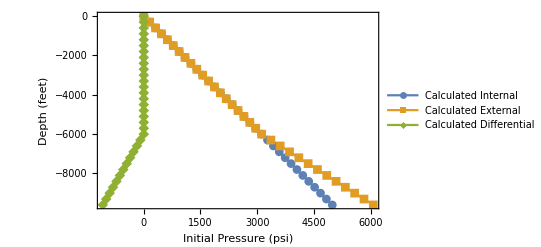

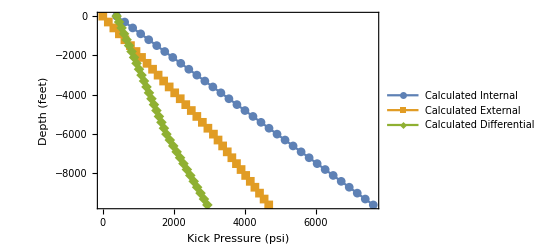

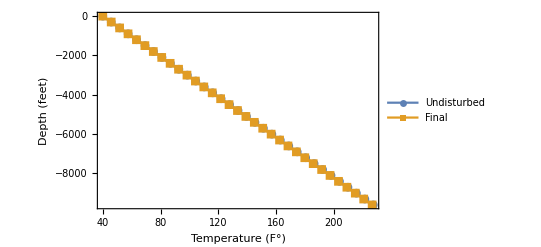

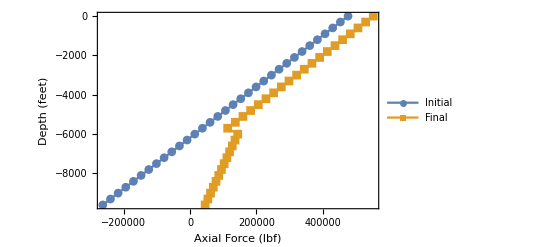

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
(*Step Size*)
dl=300;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=77;
de=13.375;
di=12.275;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};

(*Initial Conditions Data*)
diplacefluid=10;
cementslurry=15.8;
previousfasefluid=10;
L0=0.;
Lf=9700.;
TOC=6000.;
Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl};

(*Kick Data*)
FracDepth=15000;
FracDensity=15.81;
MaxMudDensity=14.5;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=10;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};

(*Temperature Data*)
Tfini=227.3;
T0fim=40.;
Tf=226.5;
T0=40.;

(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,Lvec,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0fim,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0,Tf,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plot Routine*)
ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Initial Pressure (psi)",""}},PlotLegends->{"Calculated Internal","Calculated External","Calculated Differential"},PlotMarkers->Automatic]
ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Kick Pressure (psi)",""}},PlotLegends->{"Calculated Internal","Calculated External","Calculated Differential"},PlotMarkers->Automatic]
ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)",""}},PlotLegends->{"Undisturbed","Final"},PlotMarkers->Automatic]
ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Axial Force (lbf)",""}},PlotLegends->{"Initial","Final"},PlotMarkers->Automatic]
```

```mathematica
(*Dados das variáveis aleatórias do modelo de Klever Stewart -  ISO 10400*)
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];

(*Dados do tubular - (N80,OD=9 5/8, W=53.5 lb/ft, L =15000 ft*)
vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];
```

```mathematica
(*FORM Para Klever-Stewart*)
plotbetaKS=Table[{HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
plotbetaKSi=Table[{iHRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
(*Fator de Segurança Para Klever-Stewart*)
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{SFBarlow,SFKS,plotbetaKS,plotbetaKSi},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Barlow SF","Klever-Stewart Safety Factor","Reliability Index HRLF","Reliability Index iHRLF"},PlotMarkers->{"X","O"}]
```

| iter = 2  | residual = 0. | G(x) = 7005.64| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6947.89| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6889.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6830.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6771.27| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6711.28| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6650.75| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6589.68| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6528.06| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6465.91| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6403.23| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6340.02| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6276.28| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6212.02| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6147.23| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6081.93| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 6016.1| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5949.77| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5882.91| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5815.55| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5741.67| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5646.61| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5551.49| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5456.3| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5361.05| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5265.73| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5170.35| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 5074.9| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 4979.39| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 4883.82| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 4788.18| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 4692.47| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 4596.71| Beta = 0.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Min::nord: Invalid comparison with 593.28+374.988 ⅈ attempted.

Min::nord: Invalid comparison with 0.+749.976 ⅈ attempted.

Min::nord: Invalid comparison with 593.28+374.988 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.-726.679 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

| iter = 7  | residual = 0.000655613 | G(x) = -389.398 | alfa = 0.00012207| kn = 13| Beta = 26.2496

| iter = 32  | residual = 0.000279004 | G(x) = 1.55873 | alfa = 0.5| kn = 1| Beta = 17.144

| iter = 7  | residual = 0.000393814 | G(x) = -528.798 | alfa = 0.0000305176| kn = 15| Beta = 26.667

| iter = 10  | residual = 0.000713859 | G(x) = -1.00527 | alfa = 1.| kn = 0| Beta = 17.6026

| iter = 17  | residual = 0.0000616424 | G(x) = 3.83578 | alfa = 1| kn = -2| Beta = 17.8092

| iter = 16  | residual = 0.0000572831 | G(x) = 3184.51 | alfa = 0.000488281| kn = 11| Beta = 12.408

| iter = 24  | residual = 0.000467546 | G(x) = 1.35374 | alfa = 0.5| kn = 1| Beta = 18.188

| iter = 28  | residual = 0.000898834 | G(x) = 14.0196 | alfa = 0.125| kn = 3| Beta = 18.5418

| iter = 13  | residual = 0.000393911 | G(x) = 18.0519 | alfa = 0.0625| kn = 4| Beta = 18.306

| iter = 14  | residual = 0.0000201808 | G(x) = 10.1534 | alfa = 0.03125| kn = 5| Beta = 18.0642

| iter = 41  | residual = 0.000965649 | G(x) = 2.51706 | alfa = 0.25| kn = 2| Beta = 17.8345

| iter = 19  | residual = 0.000895385 | G(x) = 6.38091 | alfa = 0.25| kn = 2| Beta = 17.5895

| iter = 14  | residual = 0.0000539652 | G(x) = 8.06156 | alfa = 0.0625| kn = 4| Beta = 17.3387

| iter = 15  | residual = 0.000188361 | G(x) = 4.67691 | alfa = 0.25| kn = 2| Beta = 17.0914

| iter = 15  | residual = 0.0000445496 | G(x) = 5.05107 | alfa = 0.125| kn = 3| Beta = 16.8389

| iter = 33  | residual = 0.000958556 | G(x) = 1.52099 | alfa = 0.125| kn = 3| Beta = 16.5988

| iter = 14  | residual = 0.000314677 | G(x) = -0.0151923 | alfa = 0.015625| kn = 6| Beta = 16.3694

| iter = 20  | residual = 0.000518183 | G(x) = 0.777528 | alfa = 1.| kn = 0| Beta = 16.0687

| iter = 20  | residual = 0.000326818 | G(x) = 0.752366 | alfa = 1.| kn = 0| Beta = 15.8062

| iter = 20  | residual = 0.000839144 | G(x) = -0.1066 | alfa = 1.| kn = 0| Beta = 15.5449

| iter = 12  | residual = 0.000607231 | G(x) = 5.51282 | alfa = 0.25| kn = 2| Beta = 15.2836

| iter = 13  | residual = 0.000230506 | G(x) = 2.10852 | alfa = 0.5| kn = 1| Beta = 14.9081

| iter = 13  | residual = 0.000523767 | G(x) = 2.67599 | alfa = 0.25| kn = 2| Beta = 14.5329

| iter = 13  | residual = 0.000850078 | G(x) = 2.76269 | alfa = 0.25| kn = 2| Beta = 14.1629

| iter = 14  | residual = 0.00089662 | G(x) = 2.44745 | alfa = 0.25| kn = 2| Beta = 13.7994

| iter = 15  | residual = 0.000722465 | G(x) = 0.854628 | alfa = 0.5| kn = 1| Beta = 13.4456

| iter = 15  | residual = 0.000827263 | G(x) = 0.864968 | alfa = 0.5| kn = 1| Beta = 13.0936

| iter = 15  | residual = 0.000881963 | G(x) = 0.865025 | alfa = 0.5| kn = 1| Beta = 12.7475

| iter = 15  | residual = 0.000904112 | G(x) = 0.85811 | alfa = 0.5| kn = 1| Beta = 12.4074

| iter = 15  | residual = 0.000905305 | G(x) = 0.846489 | alfa = 0.5| kn = 1| Beta = 12.0732

| iter = 15  | residual = 0.00089316 | G(x) = 0.831708 | alfa = 0.5| kn = 1| Beta = 11.7448

| iter = 15  | residual = 0.000872673 | G(x) = 0.814823 | alfa = 0.5| kn = 1| Beta = 11.422

| iter = 15  | residual = 0.000847114 | G(x) = 0.796557 | alfa = 0.5| kn = 1| Beta = 11.1048

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

# Caso de kick revestimento de superfície

-Graphics-

Interpolation::inddp: The point 43422. in dimension 1 is duplicated.

int = ∫_0^440. Interpolation[{{43422.,0.},{43422.,-10.},{43422.,-20.},{43422.,-30.},{43422.,-40.},{43422.,-50.},{43422.,-60.},{43422.,-70.},{43422.,-80.},{43422.,-90.},{43422.,-100.},{43422.,-110.},{43422.,-120.},{43422.,-130.},{43422.,-140.},{43422.,-150.},{43422.,-160.},{43422.,-170.},{43422.,-180.},{43422.,-190.},{43422.,-200.},{43422.,-210.},{43422.,-220.},{43422.,-230.},{43422.,-240.},{43422.,-250.},{43422.,-260.},{43422.,-270.},{43422.,-280.},{43422.,-290.},{43422.,-300.},{43422.,-310.},{43422.,-320.},{43422.,-330.},{43422.,-340.},{43422.,-350.},{43422.,-360.},{43422.,-370.},{43422.,-380.},{43422.,-390.},{43422.,-400.},{43422.,-410.},{43422.,-420.},{43422.,-430.},{43422.,-440.}}][x]ⅆx

Sum[Fballoning[[j]],{j,1,i}]/i = 43422.

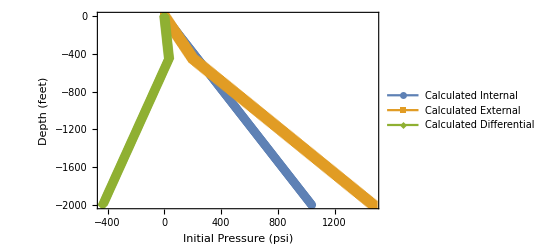

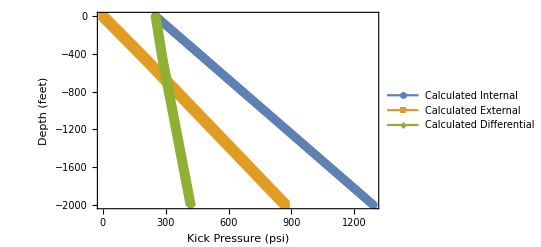

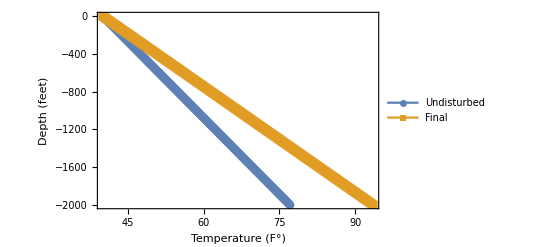

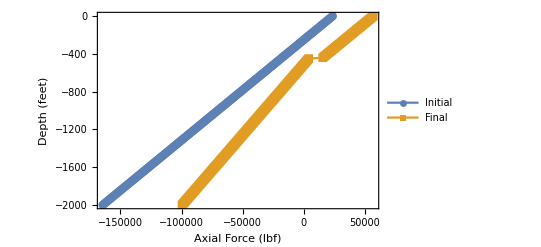

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
(*Step Size*)
dl=10;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=94;
de=20;
di=19.124;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=55000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};

(*Initial Conditions Data*)
diplacefluid=10;
cementslurry=15.8;
previousfasefluid=8.6;
L0=0.;
Lf=2000.;
TOC=450.;
Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl};

(*Kick Data*)
FracDepth=9700;
FracDensity=14.29;
MaxMudDensity=10.;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=8.6;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};

(*Temperature Data*)
Tfini=77.1;
T0fim=40.;
Tf=93.6;
T0=40.;

(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,Lvec,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0fim,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0,Tf,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plot Routine*)
ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Initial Pressure (psi)",""}},PlotLegends->{"Calculated Internal","Calculated External","Calculated Differential"},PlotMarkers->Automatic]
ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Kick Pressure (psi)",""}},PlotLegends->{"Calculated Internal","Calculated External","Calculated Differential"},PlotMarkers->Automatic]
ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)",""}},PlotLegends->{"Undisturbed","Final"},PlotMarkers->Automatic]
ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Axial Force (lbf)",""}},PlotLegends->{"Initial","Final"},PlotMarkers->Automatic]
```

```mathematica
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.01},{"Pext","NORMAL",1.0,0.01},{"Pint","NORMAL",1.0,0.01}};
(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];

(*Dados do tubular - (N80,OD=9 5/8, W=53.5 lb/ft, L =15000 ft*)
vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];
```

```mathematica
(*FORM Para Klever-Stewart*)
plotbetaKS=Table[{HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
plotbetaKSi=Table[{iHRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
(*Fator de Segurança Para Klever-Stewart*)
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{SFBarlow,SFKS,plotbetaKS,plotbetaKSi},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Barlow SF","Klever-Stewart Safety Factor","Reliability Index HRLF","Reliability Index iHRLF"},PlotMarkers->{"X","O"}]
```

| iter = 2  | residual = 0. | G(x) = 2379.12| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2378.41| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2377.71| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2377.01| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2376.3| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2375.6| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2374.9| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2374.19| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2373.48| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2372.78| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2372.07| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2371.37| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2370.66| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2369.95| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2369.24| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2368.54| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2367.83| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2367.12| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2366.41| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2365.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2364.99| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2364.28| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2363.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2362.86| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2362.14| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2361.43| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2360.72| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2360.01| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2359.29| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2358.58| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2357.86| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2357.15| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2356.43| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2355.72| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2355.| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2354.29| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2353.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2352.85| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2352.13| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2351.42| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2350.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2349.98| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2349.26| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2348.54| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2347.82| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2347.14| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2346.28| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2345.41| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2344.54| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2343.68| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2342.81| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2341.94| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2341.08| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2340.21| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2339.34| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2338.47| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2337.6| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2336.73| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2335.87| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2335.| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2334.13| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2333.26| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2332.39| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2331.52| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2330.65| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2329.78| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2328.91| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2328.04| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2327.16| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2326.29| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2325.42| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2324.55| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2323.68| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2322.81| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2321.93| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2321.06| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2320.19| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2319.32| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2318.44| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2317.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2316.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2315.82| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2314.95| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2314.07| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2313.2| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2312.33| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2311.45| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2310.58| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2309.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2308.83| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2307.95| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2307.07| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2306.2| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2305.32| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2304.45| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2303.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2302.69| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2301.82| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2300.94| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2300.06| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2299.18| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2298.3| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2297.43| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2296.55| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2295.67| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2294.79| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2293.91| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2293.03| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2292.15| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2291.27| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2290.39| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2289.51| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2288.63| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2287.75| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2286.87| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2285.99| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2285.11| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2284.23| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2283.35| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2282.47| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2281.58| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2280.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2279.82| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2278.94| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2278.06| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2277.17| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2276.29| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2275.41| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2274.52| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2273.64| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2272.75| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2271.87| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2270.99| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2270.1| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2269.22| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2268.33| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2267.45| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2266.56| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2265.68| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2264.79| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2263.9| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2263.02| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2262.13| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2261.24| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2260.36| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2259.47| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2258.58| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2257.69| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2256.81| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2255.92| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2255.03| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2254.14| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2253.25| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2252.37| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2251.48| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2250.59| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2249.7| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2248.81| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2247.92| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2247.03| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2246.14| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2245.25| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2244.36| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2243.47| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2242.57| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2241.68| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2240.79| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2239.9| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2239.01| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2238.12| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2237.22| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2236.33| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2235.44| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2234.54| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2233.65| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2232.76| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2231.86| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2230.97| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2230.08| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2229.18| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2228.29| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2227.39| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2226.5| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2225.6| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2224.71| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2223.81| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2222.92| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2222.02| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2221.12| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2220.23| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2219.33| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2218.43| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2217.54| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2216.64| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2215.74| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2214.85| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2213.95| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2213.05| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2212.15| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2211.25| Beta = 0.

| iter = 2  | residual = 0. | G(x) = 2210.35| Beta = 0.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

| iter = 52  | residual = 0.000910647 | G(x) = 4.11154 | alfa = 0.125| kn = 3| Beta = 19.0965

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

| iter = 52  | residual = 0.000916402 | G(x) = 4.12077 | alfa = 0.125| kn = 3| Beta = 19.0897

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

| iter = 52  | residual = 0.000933151 | G(x) = 4.12224 | alfa = 0.125| kn = 3| Beta = 19.083

| iter = 52  | residual = 0.000939001 | G(x) = 4.1317 | alfa = 0.125| kn = 3| Beta = 19.0761

| iter = 52  | residual = 0.000944892 | G(x) = 4.14126 | alfa = 0.125| kn = 3| Beta = 19.0693

| iter = 52  | residual = 0.000950826 | G(x) = 4.15093 | alfa = 0.125| kn = 3| Beta = 19.0624

| iter = 87  | residual = 0.000956628 | G(x) = 5.79626 | alfa = 0.0625| kn = 4| Beta = 19.0605

| iter = 87  | residual = 0.000960081 | G(x) = 5.80713 | alfa = 0.0625| kn = 4| Beta = 19.0536

| iter = 87  | residual = 0.000963554 | G(x) = 5.81809 | alfa = 0.0625| kn = 4| Beta = 19.0467

| iter = 87  | residual = 0.000967048 | G(x) = 5.82914 | alfa = 0.0625| kn = 4| Beta = 19.0399

| iter = 87  | residual = 0.000976864 | G(x) = 5.83169 | alfa = 0.0625| kn = 4| Beta = 19.0331

| iter = 87  | residual = 0.000980406 | G(x) = 5.84292 | alfa = 0.0625| kn = 4| Beta = 19.0262

| iter = 87  | residual = 0.000983968 | G(x) = 5.85424 | alfa = 0.0625| kn = 4| Beta = 19.0193

| iter = 8  | residual = 0.000917046 | G(x) = 47.0093 | alfa = 0.0625| kn = 4| Beta = 19.4987

| iter = 8  | residual = 0.000789615 | G(x) = 47.0107 | alfa = 0.0625| kn = 4| Beta = 19.4885

| iter = 8  | residual = 0.000662708 | G(x) = 47.0118 | alfa = 0.0625| kn = 4| Beta = 19.4784

| iter = 8  | residual = 0.000536329 | G(x) = 47.0125 | alfa = 0.0625| kn = 4| Beta = 19.4682

| iter = 8  | residual = 0.000410482 | G(x) = 47.0128 | alfa = 0.0625| kn = 4| Beta = 19.458

| iter = 8  | residual = 0.00028517 | G(x) = 47.0126 | alfa = 0.0625| kn = 4| Beta = 19.4478

| iter = 8  | residual = 0.000160396 | G(x) = 47.0121 | alfa = 0.0625| kn = 4| Beta = 19.4376

| iter = 8  | residual = 0.000108294 | G(x) = 47.7898 | alfa = 0.03125| kn = 5| Beta = 19.4273

| iter = 8  | residual = 0.0000459195 | G(x) = 47.7883 | alfa = 0.03125| kn = 5| Beta = 19.417

| iter = 8  | residual = 0.0000161795 | G(x) = 47.7863 | alfa = 0.03125| kn = 5| Beta = 19.4067

| iter = 8  | residual = 0.0000780013 | G(x) = 47.784 | alfa = 0.03125| kn = 5| Beta = 19.3964

| iter = 8  | residual = 0.000139544 | G(x) = 47.7813 | alfa = 0.03125| kn = 5| Beta = 19.386

| iter = 8  | residual = 0.000200807 | G(x) = 47.7782 | alfa = 0.03125| kn = 5| Beta = 19.3757

| iter = 8  | residual = 0.000109134 | G(x) = 48.1579 | alfa = 0.015625| kn = 6| Beta = 19.3652

| iter = 8  | residual = 0.000139614 | G(x) = 48.1539 | alfa = 0.015625| kn = 6| Beta = 19.3548

| iter = 8  | residual = 0.000169951 | G(x) = 48.1495 | alfa = 0.015625| kn = 6| Beta = 19.3444

| iter = 8  | residual = 0.0000947305 | G(x) = 48.3349 | alfa = 0.0078125| kn = 7| Beta = 19.3339

| iter = 8  | residual = 0.0000535665 | G(x) = 48.4244 | alfa = 0.00390625| kn = 8| Beta = 19.3234

| iter = 8  | residual = 0.0000302037 | G(x) = 48.466 | alfa = 0.00195313| kn = 9| Beta = 19.313

| iter = 42  | residual = 0.00086727 | G(x) = 0.365693 | alfa = 0.5| kn = 1| Beta = 18.8751

| iter = 42  | residual = 0.000875539 | G(x) = 0.369506 | alfa = 0.5| kn = 1| Beta = 18.8679

| iter = 42  | residual = 0.000883903 | G(x) = 0.373369 | alfa = 0.5| kn = 1| Beta = 18.8606

| iter = 42  | residual = 0.000892363 | G(x) = 0.377281 | alfa = 0.5| kn = 1| Beta = 18.8534

| iter = 43  | residual = 0.000816302 | G(x) = 0.345368 | alfa = 0.5| kn = 1| Beta = 18.8464

| iter = 43  | residual = 0.000824265 | G(x) = 0.349055 | alfa = 0.5| kn = 1| Beta = 18.8391

| iter = 43  | residual = 0.000832321 | G(x) = 0.352791 | alfa = 0.5| kn = 1| Beta = 18.8318

| iter = 43  | residual = 0.000840469 | G(x) = 0.356575 | alfa = 0.5| kn = 1| Beta = 18.8245

| iter = 43  | residual = 0.000848712 | G(x) = 0.360408 | alfa = 0.5| kn = 1| Beta = 18.8172

| iter = 43  | residual = 0.000857048 | G(x) = 0.364291 | alfa = 0.5| kn = 1| Beta = 18.8099

| iter = 43  | residual = 0.00086548 | G(x) = 0.368225 | alfa = 0.5| kn = 1| Beta = 18.8025

| iter = 43  | residual = 0.000991861 | G(x) = 0.422568 | alfa = 0.5| kn = 1| Beta = 18.7947

| iter = 44  | residual = 0.000800756 | G(x) = 0.341274 | alfa = 0.5| kn = 1| Beta = 18.7881

| iter = 44  | residual = 0.000808193 | G(x) = 0.344774 | alfa = 0.5| kn = 1| Beta = 18.7808

| iter = 44  | residual = 0.00081748 | G(x) = 0.349121 | alfa = 0.5| kn = 1| Beta = 18.7721

| iter = 44  | residual = 0.000826877 | G(x) = 0.353527 | alfa = 0.5| kn = 1| Beta = 18.7634

| iter = 44  | residual = 0.000836383 | G(x) = 0.357992 | alfa = 0.5| kn = 1| Beta = 18.7547

| iter = 32  | residual = 0.000790698 | G(x) = 1.9214 | alfa = 0.25| kn = 2| Beta = 18.7444

| iter = 32  | residual = 0.000799592 | G(x) = 1.93414 | alfa = 0.25| kn = 2| Beta = 18.7357

| iter = 32  | residual = 0.000808582 | G(x) = 1.94693 | alfa = 0.25| kn = 2| Beta = 18.727

| iter = 32  | residual = 0.00081767 | G(x) = 1.95977 | alfa = 0.25| kn = 2| Beta = 18.7182

| iter = 32  | residual = 0.000826856 | G(x) = 1.97266 | alfa = 0.25| kn = 2| Beta = 18.7095

| iter = 32  | residual = 0.000836139 | G(x) = 1.98559 | alfa = 0.25| kn = 2| Beta = 18.7007

| iter = 32  | residual = 0.00084552 | G(x) = 1.99857 | alfa = 0.25| kn = 2| Beta = 18.6919

| iter = 32  | residual = 0.000855 | G(x) = 2.01159 | alfa = 0.25| kn = 2| Beta = 18.6831

| iter = 32  | residual = 0.000864577 | G(x) = 2.02465 | alfa = 0.25| kn = 2| Beta = 18.6743

| iter = 32  | residual = 0.000874253 | G(x) = 2.03775 | alfa = 0.25| kn = 2| Beta = 18.6655

Min::nord: Invalid comparison with 0.-1.65398 ⅈ attempted.

Min::nord: Invalid comparison with -2.58271-0.826989 ⅈ attempted.

Min::nord: Invalid comparison with 0.-1.65398 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

| iter = 32  | residual = 0.000884026 | G(x) = 2.05089 | alfa = 0.25| kn = 2| Beta = 18.6567

| iter = 32  | residual = 0.000893898 | G(x) = 2.06406 | alfa = 0.25| kn = 2| Beta = 18.6478

| iter = 32  | residual = 0.000903868 | G(x) = 2.07728 | alfa = 0.25| kn = 2| Beta = 18.639

| iter = 32  | residual = 0.000913935 | G(x) = 2.09052 | alfa = 0.25| kn = 2| Beta = 18.6301

| iter = 32  | residual = 0.0009241 | G(x) = 2.1038 | alfa = 0.25| kn = 2| Beta = 18.6212

| iter = 32  | residual = 0.000934362 | G(x) = 2.11711 | alfa = 0.25| kn = 2| Beta = 18.6124

| iter = 21  | residual = 0.000898935 | G(x) = 0.392496 | alfa = 0.5| kn = 1| Beta = 18.6048

| iter = 21  | residual = 0.000910635 | G(x) = 0.398117 | alfa = 0.5| kn = 1| Beta = 18.5959

| iter = 21  | residual = 0.00092248 | G(x) = 0.403818 | alfa = 0.5| kn = 1| Beta = 18.5869

| iter = 21  | residual = 0.000934471 | G(x) = 0.409602 | alfa = 0.5| kn = 1| Beta = 18.5779

| iter = 21  | residual = 0.000946609 | G(x) = 0.415469 | alfa = 0.5| kn = 1| Beta = 18.5689

$Aborted

-Graphics-